## Preamble

```mathematica
LaunchKernels[10];
<< KerrGeodesics`
<< GeneralRelativityTensors`
<<SpinWeightedSpheroidalHarmonics`
<<Teukolsky`
ParallelNeeds["SpinWeightedSpheroidalHarmonics`"];
ParallelNeeds["Teukolsky`"];
ParallelNeeds["KerrGeodesics`"];
Information[PacletObject["Teukolsky"]]
```

Paclet

## Calculating ϕ_1

## Calculating homogenous Φ_1 given a radius r

```mathematica
ϕ1[r_,a_,p_,e_, l_,m_,n_]:=Module[{Ω,ω, Σ, Δ, Trad, Tradmino, orbit, t0,r0,θ0, ϕ0, Q0,K0,Β, λ, prec=32},
Σ=r^2+a^2 Cos[θ]^2;
Δ=r^2-2 M r + a^2;
Ω= KerrGeoFrequencies[a,p,e,1];
ω=m Ω[[3]] + n Ω[[1]];
Trad =2π/Ω[[1]];
Tradmino=2π/KerrGeoFrequencies[a,p,e,1,Time->"Mino"][[1]];
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],SetPrecision[1,prec]];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
Q0 := m-a ω[m,n];
K0[λ_]:= ω[m,n](r0[λ]^2 + a^2)- a m;
λ = SpinWeightedSpheroidalEigenvalue[1,l,m,a ω];
Β= Sqrt[λ^2+ 4 a m ω - 4 a^2 ω^2];

(*To Do: calculate g_(+1) and Subscript[f, -1] and then combine them to calculate Subscript[ϕ, 1]*)
]
```

```mathematica
Φ1[a_ ,p_,e_,τmino_,  r_,l_,m_,n_]:=Module[{Ω,α,ω,P,dP, S,R,expFactor,Q0,K0,λ,Β,g,f,orbit,numberOfRs,LS, t0,r0,θ0,ϕ0, rmax,rmin,outputlist, Δ,M=1,prec=32},
Ω= KerrGeoFrequencies[a,p,e,SetPrecision[1,prec]];
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
{rmax,rmin} =OrbitTP[p,e];
ω= m Ω[[3]] + n Ω[[1]];
Δ = r^2-2 M r + a^2;
Q0 = m-a ω;
K0= ω(r + a^2)- a m;
λ = SpinWeightedSpheroidalEigenvalue[-1,l,m,a ω];
R = TeukolskyRadial[1,l,m,a, ω];
P=R["In"][r];
dP =R["In"]'[r];
Β= Sqrt[λ^2+ 4 a m ω - 4 a^2 ω^2];
LS = SpinWeightedSpheroidalHarmonicS[1,l,m,a ω];
g= 1/Β (r dP- ⅈ K0 r/Δ P-P);
f = 1/Β(Cos[θ0[τmino]](ReplaceAll[D[LS[θ,ϕ0[τmino]],θ],θ->θ0[τmino]]+ Q0 LS[θ0[τmino], ϕ0[τmino]] + LS[θ0[τmino], ϕ0[τmino]] Cot[θ0[τmino]]) + Sin[θ0[τmino]] LS[θ0[τmino], ϕ0[τmino]] );
expFactor = Exp[-ⅈ ω t0[τmino] + ⅈ m ϕ0[τmino]];

 expFactor/(Sqrt[2] (r - ⅈ a Cos[θ0[τmino]])^2)(g (ReplaceAll[D[LS[θ,ϕ0[τmino]],θ],θ->θ0[τmino]]+ Q0 LS[θ0[τmino], ϕ0[τmino]] + LS[θ0[τmino], ϕ0[τmino]] Cot[θ0[τmino]]) - ⅈ a f  (dP- ⅈ K0/Δ P))
];
```

```mathematica
Module[{ω,Ω, l=1,m=0,n=0},
ω= m Ω[[3]] + n Ω[[1]];
]
```

```mathematica
Φ1[0 ,10,0.1,0.5, 7,1,0,0]
```

0.+0. ⅈ

{-0.00236851+0. ⅈ,-0.00216822+0. ⅈ,-0.0019923+0. ⅈ,-0.00183696+0. ⅈ,-0.0016991+0. ⅈ,-0.00157619+0. ⅈ,-0.00146616+0. ⅈ,-0.00136725+0. ⅈ,-0.00127803+0. ⅈ,-0.00119726+0. ⅈ,-0.00112392+0. ⅈ,-0.00105711+0. ⅈ,-0.000996092+0. ⅈ,-0.000940206+0. ⅈ,-0.000888894+0. ⅈ,-0.000841671+0. ⅈ,-0.000798113+0. ⅈ,-0.000757851+0. ⅈ,-0.000720561+0. ⅈ,-0.000685957+0. ⅈ,-0.000653787+0. ⅈ,-0.000623828+0. ⅈ,-0.000595882+0. ⅈ,-0.000569772+0. ⅈ,-0.000545342+0. ⅈ,-0.00052245+0. ⅈ,-0.00050097+0. ⅈ,-0.000480788+0. ⅈ,-0.000461801+0. ⅈ,-0.000443918+0. ⅈ,-0.000427053+0. ⅈ,-0.000411131+0. ⅈ,-0.000396084+0. ⅈ,-0.000381847+0. ⅈ,-0.000368365+0. ⅈ,-0.000355584+0. ⅈ,-0.000343458+0. ⅈ,-0.000331941+0. ⅈ,-0.000320993+0. ⅈ,-0.000310579+0. ⅈ,-0.000300663+0. ⅈ,-0.000291215+0. ⅈ,-0.000282205+0. ⅈ,-0.000273607+0. ⅈ,-0.000265396+0. ⅈ,-0.000257549+0. ⅈ,-0.000250045+0. ⅈ,-0.000242864+0. ⅈ,-0.000235988+0. ⅈ,-0.000229401+0. ⅈ,-0.000223085+0. ⅈ}

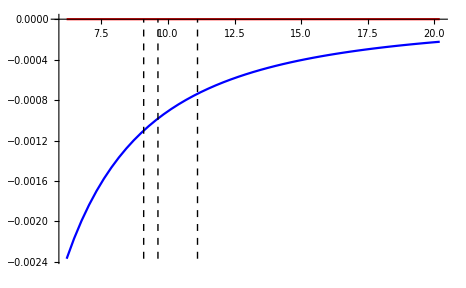

```mathematica
Module[{rmax, rmin,rdata ,Φdata,lineStyle, line1, line2, line3, AllData, orbit, t0, r0, θ0, ϕ0,  numpts = 100,  a=0,p=10,e=0.1,τmino = 0.5,l=2,m=0, n=0, prec=32},
{rmax,rmin} =OrbitTP[p,e];
rdata = Subdivide[KerrGeoSeparatrix[a,e,1], rmin+rmax,numpts/2];
Φdata = ParallelTable [Φ1[a,p,e,τmino,rdata[[i]],l,m,n],{i,1,Length[rdata]}];
Print[Φdata];
AllData = Flatten[{Re[Φdata],Im[Φdata]}];
lineStyle={Thick,Black,Dashed};
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
lineStyle={Thick,Black,Dashed};
line1=Line[{{rmin,Min[AllData]},{rmin,Max[AllData]}}];line2=Line[{{rmax,Min[AllData]},{rmax,Max[AllData]}}];
line3= Line[{{r0[τmino],Min[AllData]},{r0[τmino],Max[AllData]}}];
ListPlot[{Table[{rdata[[i]], Re[Φdata[[i]]]},{i,1,Length[rdata]}],Table[{rdata[[i]], Im[Φdata[[i]]]},{i,1,Length[rdata]}]}, PlotStyle->{Blue, Red}, Joined->True,Epilog->{Directive[lineStyle],line1,line2,line3}]
]
```

## Calculating ϕ_0 and ϕ_2

```mathematica
OrbitTP[p_,e_]:= Module[{},{rMax, rMin}/.NSolve[{p== (2 rMax rMin)/(rMax + rMin), e == (rMax-rMin)/(rMax + rMin)}, {rMax, rMin}][[1]]]
```

```mathematica
LMAX = 5;NMAX=2;
```

```mathematica
Φ0[a_ ,p_,e_,τmino_,  r_,l_]:=Module[{Ω,orbit,numberOfRs, t0,r0,θ0,ϕ0, rmax,rmin,outputlist, Δ, sum,M=1,prec=32},
Ω= KerrGeoFrequencies[a,p,e,SetPrecision[1,prec]];
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
{rmax,rmin} =OrbitTP[p,e];

numberOfRs = Length[r];
If[numberOfRs==0, 
Δ=r^2-2 M r + a^2;
If[r>= r0[τmino],
sum =Table[
Module[{α,ω,P,S,R,expFactor},
ω= m Ω[[3]] + n Ω[[1]];
R = TeukolskyRadial[1,l,m,a, ω];
P=R["Up"][r]Δ;
α = TeukolskyPointParticleMode[1 , l,m,n,0,orbit]["Amplitudes"]["ℐ"]; 
S=SpinWeightedSpheroidalHarmonicS[1,l,m,a ω][θ0[τmino], ϕ0[τmino]];
expFactor = Exp[-ⅈ ω t0[τmino] + ⅈ m ϕ0[τmino]];
S expFactor α P
]
,{m,-l,l},{n,-NMAX,NMAX}
];
];
If[r<= r0[τmino],
sum =Table[
Module[{α,ω,P,S,R,expFactor},
ω= m Ω[[3]] + n Ω[[1]];
R = TeukolskyRadial[1,l,m,a, ω];
P=R["In"][r];
α = TeukolskyPointParticleMode[1 , l,m,n,0,orbit]["Amplitudes"]["ℋ"]; 
S=SpinWeightedSpheroidalHarmonicS[1,l,m,a ω][θ0[τmino], ϕ0[τmino]];
expFactor = Exp[-ⅈ ω t0[τmino] + ⅈ m ϕ0[τmino]];
S expFactor α P
]
,{m,-l,l},{n,-NMAX,NMAX}
];
];
 Δ^-1 Total[Flatten[sum]],
(*If r is a list*)
outputlist=Table[0,{i,1,numberOfRs}];
Module[{m,n,R, ω,mode,α,S,P,i, expFactor},
m=-l;
While[m<=l,
n=-NMAX;
While[n<=NMAX,
ω= m Ω[[3]] + n Ω[[1]];
R= TeukolskyRadial[1,l,m,a, ω];
mode =TeukolskyPointParticleMode[1 , l,m,n,0,orbit];
S=SpinWeightedSpheroidalHarmonicS[1,l,m,a ω][θ0[τmino], ϕ0[τmino]];
expFactor = Exp[-ⅈ ω t0[τmino] + ⅈ m ϕ0[τmino]];
i = 1;
While[i<=numberOfRs,
Δ=r[[i]]^2-2 M r[[i]] + a^2;
If[r[[i]]>=r0[τmino],
P=R["Up"][r[[i]]]Δ;
α=mode["Amplitudes"]["ℐ"];
outputlist[[i]]=outputlist[[i]]+Δ^-1 S expFactor α P,
P=R["In"][r[[i]]];
α=mode["Amplitudes"]["ℋ"];
outputlist[[i]]=outputlist[[i]]+Δ^-1 S expFactor α P,
];
i=i+1;
];
n=n+1;
];
m=m+1;
];
];
outputlist
]
]
```

```mathematica
Φ2 [a_ , r_ ,τmino_, p_,e_,l_]:= Module[{Δ,Ω,orbit, rmin, rmax,sum,t0,r0,θ0,ϕ0, M=1,prec= 32},
Δ=r^2-2 M r + a^2;
Ω= KerrGeoFrequencies[a,p,e,SetPrecision[1,prec]];
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
{rmax,rmin} =OrbitTP[p,e];
If[r>= r0[τmino],
sum =Table[
Module[{α,ω,P,S,R,expFactor},
ω= m Ω[[3]] + n Ω[[1]];
R = TeukolskyRadial[-1,l,m,a, ω];
P=R["Up"][r]Δ;
α = TeukolskyPointParticleMode[-1 , l,m,n,0,orbit]["Amplitudes"]["ℐ"]; 
S=SpinWeightedSpheroidalHarmonicS[-1,l,m,a ω][θ0[τmino], ϕ0[τmino]];
expFactor = Exp[-ⅈ ω t0[τmino] + ⅈ m ϕ0[τmino]];
S expFactor α P
]
,{m,-l,l},{n,-NMAX,NMAX}
];
];
If[r<= r0[τmino],
sum =Table[
Module[{α,ω,P,S,R,expFactor},
ω= m Ω[[3]] + n Ω[[1]];
R = TeukolskyRadial[-1,l,m,a, ω];
P=R["In"][r]Δ;
α = TeukolskyPointParticleMode[-1 , l,m,n,0,orbit]["Amplitudes"]["ℋ"]; 
S=SpinWeightedSpheroidalHarmonicS[-1,l,m,a ω][θ0[τmino], ϕ0[τmino]];
expFactor = Exp[-ⅈ ω t0[τmino] + ⅈ m ϕ0[τmino]];
S expFactor α P
]
,{m,-l,l},{n,-NMAX,NMAX}
];
];
1/(2(r-ⅈ a Cos[θ0[τmino]])^2)Δ^-1 Total[Flatten[sum]]
]
```

```mathematica
Φ2[a_ ,p_,e_,τmino_,  r_,l_]:=Module[{Ω,orbit,numberOfRs, t0,r0,θ0,ϕ0, rmax,rmin,outputlist, Δ, sum,M=1,prec=32},
Ω= KerrGeoFrequencies[a,p,e,SetPrecision[1,prec]];
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
{rmax,rmin} =OrbitTP[p,e];

numberOfRs = Length[r];
If[numberOfRs==0, 
Δ=r^2-2 M r + a^2;
If[r>= r0[τmino],
sum =Table[
Module[{α,ω,P,S,R,expFactor},
ω= m Ω[[3]] + n Ω[[1]];
R = TeukolskyRadial[-1,l,m,a, ω];
P=R["Up"][r]Δ;
α = TeukolskyPointParticleMode[-1 , l,m,n,0,orbit]["Amplitudes"]["ℐ"]; 
S=SpinWeightedSpheroidalHarmonicS[-1,l,m,a ω][θ0[τmino], ϕ0[τmino]];
expFactor = Exp[-ⅈ ω t0[τmino] + ⅈ m ϕ0[τmino]];
S expFactor α P
]
,{m,-l,l},{n,-NMAX,NMAX}
];
];
If[r<= r0[τmino],
sum =Table[
Module[{α,ω,P,S,R,expFactor},
ω= m Ω[[3]] + n Ω[[1]];
R = TeukolskyRadial[1,l,m,a, ω];
P=R["In"][r]Δ;
α = TeukolskyPointParticleMode[-1 , l,m,n,0,orbit]["Amplitudes"]["ℋ"]; 
S=SpinWeightedSpheroidalHarmonicS[-1,l,m,a ω][θ0[τmino], ϕ0[τmino]];
expFactor = Exp[-ⅈ ω t0[τmino] + ⅈ m ϕ0[τmino]];
S expFactor α P
]
,{m,-l,l},{n,-NMAX,NMAX}
];
];
1/(2(r-ⅈ a Cos[θ0[τmino]])^2)Δ^-1 Total[Flatten[sum]],
(*If r is a list*)
outputlist=Table[0,{i,1,numberOfRs}];
Module[{m,n,R, ω,mode,α,S,P,i, expFactor},
m=-l;
While[m<=l,
n=-NMAX;
While[n<=NMAX,
ω= m Ω[[3]] + n Ω[[1]];
R= TeukolskyRadial[-1,l,m,a, ω];
mode =TeukolskyPointParticleMode[-1 , l,m,n,0,orbit];
S=SpinWeightedSpheroidalHarmonicS[-1,l,m,a ω][θ0[τmino], ϕ0[τmino]];
expFactor = Exp[-ⅈ ω t0[τmino] + ⅈ m ϕ0[τmino]];
i = 1;
While[i<=numberOfRs,
Δ=r[[i]]^2-2 M r[[i]] + a^2;
If[r[[i]]>=r0[τmino],
P=R["Up"][r[[i]]]Δ;
α=mode["Amplitudes"]["ℐ"];
outputlist[[i]]=outputlist[[i]]+1/(2(r[[i]]-ⅈ a Cos[θ0[τmino]])^2) Δ^-1 S expFactor α P,
P=R["In"][r[[i]]]Δ;
α=mode["Amplitudes"]["ℋ"];
outputlist[[i]]=outputlist[[i]]+1/(2(r[[i]]-ⅈ a Cos[θ0[τmino]])^2) Δ^-1 S expFactor α P,
];
i=i+1;
];
n=n+1;
];
m=m+1;
];
];
outputlist
]
]
```

## Plotting Φ_0

### Sum over l

```mathematica
Module[{rmin, rmax,a=0, p=10,e=0.1, τmino=0.5},
{rmax, rmin} = OrbitTP[p,e];
lowerRs =Subdivide[KerrGeoSeparatrix[a,e,1], rmin, 50];
upperRs = Subdivide[rmax, 20,50];
lowerΦ0 = Monitor[Table[Φ0 [a , lowerRs[[i]] ,τmino, p,e,1],{i,1 ,Length[lowerRs]}],i];
upperΦ0 =Monitor[Table[Φ0 [a , upperRs[[i]] ,τmino, p,e,1],{i,1 ,Length[lowerRs]}],50+i];
]
```

$Aborted

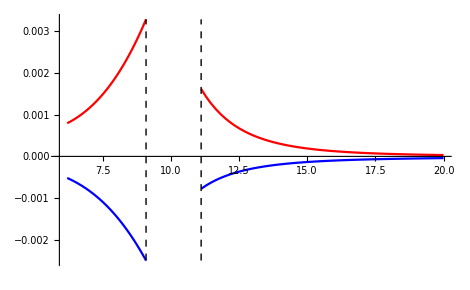

```mathematica
Module[{rmax, rmin, AllData, lineStyle, line1, line2},
{rmax, rmin} = OrbitTP[10,0.1];
AllData = Flatten[{Re[lowerΦ0],Im[lowerΦ0], Re[upperΦ0],Im[upperΦ0]}];
lineStyle={Thick,Black,Dashed};
line1=Line[{{rmin,Min[AllData]},{rmin,Max[AllData]}}];line2=Line[{{rmax,Min[AllData]},{rmax,Max[AllData]}}];
ListPlot[{Table[{lowerRs[[i]], Re[lowerΦ0[[i]]]},{i, 1 Length[lowerRs]}],Table[{lowerRs[[i]], Im[lowerΦ0[[i]]]},{i, 1 Length[lowerRs]}],Table[{upperRs[[i]], Re[upperΦ0[[i]]]},{i, 1 Length[upperRs]}],Table[{upperRs[[i]], Im[upperΦ0[[i]]]},{i, 1 Length[upperRs]}] }, Joined->True, PlotStyle->{Blue, Red,Blue,Red},
Epilog->{Directive[lineStyle],line1,line2}
]
]
```

### l = 1 mode

```mathematica
AbsoluteTiming[Module[{orbit,modes,rmin, rmax,t0,r0,θ0,ϕ0,τmino=0.5,numpts = 10,p=10,e=0.1,l=1,prec=32,a=0},
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
modes = Flatten[Table[Module[{},
TeukolskyPointParticleMode[-1,l, m,n,0,orbit]],{m,-l,l},{n,-NMAX,NMAX}]];
{rmax, rmin} = OrbitTP[p,e];
RH = Subdivide[KerrGeoSeparatrix[a,e,1],r0[τmino],numpts/2];
RI = Subdivide[r0[τmino], rmin+rmax,numpts/2];
modes[[1]]["ExtendedHomogeneous"->"ℋ"][Rs];

Φ0RH = ParallelTable[
Table[ 
modes[[j]]["ExtendedHomogeneous"->"ℋ"][RH]
,{j,1,Length[modes]}
],
{i,1, numpts/2}
];
]]
```

{11.484,Null}

```mathematica
Length[Φ0RH[[1,1]]]
```

6

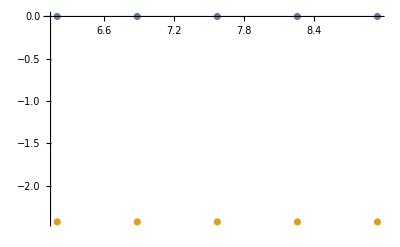

```mathematica
ListPlot[{Table[{RH[[i]],Re[Φ0RH[[i]]]},{i,1,5}],Table[{RH[[i]],Im[Φ0RH[[i]]]},{i,1,5}]}]
```

```mathematica
ClearAll[Rs]
```

```mathematica
Table[
Module[{mode},
mode = modes[[i]]
],
{i,1, Length[modes]}
]
```

```mathematica
Module[{rmin, rmax,a=0, p=10,e=0.1, τmino=0.5},
{rmax, rmin} = OrbitTP[p,e];
Rs = Subdivide[KerrGeoSeparatrix[a,e,1],rmin+rmax,200];
Φ0s= Φ0New[a,p,e,τmino,  Rs,1]
]
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in Teukolsky`ConvolveSource`Private`qr in the region {{0,3.14159265358979323846264338}}. NIntegrate obtained -1.03193063808454615648987407×10^-9+4.39808692129264290217410513×10^-11 ⅈ and 5.82906267031152836497215188×10^-22 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in Teukolsky`ConvolveSource`Private`qr in the region {{0,3.14159265358979323846264338}}. NIntegrate obtained -6.86977341181469900200422969×10^-10-9.82366629721856314405026359×10^-11 ⅈ and 7.909115453650421216592844×10^-26 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in Teukolsky`ConvolveSource`Private`qr in the region {{0,3.1415926535897932384626434}}. NIntegrate obtained -1.0948880877045589974327128×10^-8+4.280195316886715637645171×10^-9 ⅈ and 4.353056122766863608488504×10^-23 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvi will be suppressed during this calculation.

{2.55005×10^-19+0.00507545 ⅈ,2.70154×10^-19+0.00507419 ⅈ,4.47312×10^-19+0.00507294 ⅈ,4.81307×10^-19+0.00507169 ⅈ,5.93503×10^-19+0.00507046 ⅈ,5.94911×10^-19+0.00506923 ⅈ,6.95304×10^-19+0.005068 ⅈ,7.94625×10^-19+0.00506678 ⅈ,9.0904×10^-19+0.00506556 ⅈ,9.94376×10^-19+0.00506435 ⅈ,1.02615×10^-18+0.00506313 ⅈ,1.0559×10^-18+0.00506192 ⅈ,1.16051×10^-18+0.0050607 ⅈ,1.24822×10^-18+0.00505949 ⅈ,1.37673×10^-18+0.00505827 ⅈ,1.50319×10^-18+0.00505706 ⅈ,1.46013×10^-18+0.00505584 ⅈ,1.46362×10^-18+0.00505462 ⅈ,1.71214×10^-18+0.00505339 ⅈ,1.75484×10^-18+0.00505216 ⅈ,1.7714×10^-18+0.00505093 ⅈ,1.94478×10^-18+0.0050497 ⅈ,2.02975×10^-18+0.00504845 ⅈ,2.07316×10^-18+0.00504721 ⅈ,2.09841×10^-18+0.00504596 ⅈ,2.25435×10^-18+0.0050447 ⅈ,2.27422×10^-18+0.00504343 ⅈ,2.25933×10^-18+0.00504216 ⅈ,2.29757×10^-18+0.00504089 ⅈ,2.46957×10^-18+0.0050396 ⅈ,2.57044×10^-18+0.00503831 ⅈ,2.62324×10^-18+0.00503702 ⅈ,2.71931×10^-18+0.00503571 ⅈ,2.79998×10^-18+0.0050344 ⅈ,2.84168×10^-18+0.00503307 ⅈ,2.94475×10^-18+0.00503174 ⅈ,2.96902×10^-18+0.0050304 ⅈ,3.11945×10^-18+0.00502906 ⅈ,3.27857×10^-18+0.0050277 ⅈ,3.1471×10^-18+0.00502633 ⅈ,3.339×10^-18+0.00502496 ⅈ,3.41163×10^-18+0.00502358 ⅈ,3.43973×10^-18+0.00502218 ⅈ,3.59324×10^-18+0.00502078 ⅈ,3.53928×10^-18+0.00501937 ⅈ,3.55272×10^-18+0.00501794 ⅈ,3.62982×10^-18+0.00501651 ⅈ,3.81755×10^-18+0.00501507 ⅈ,3.85854×10^-18+0.00501361 ⅈ,7.34122×10^-15+0.00814884 ⅈ,6.67675×10^-15+0.00793921 ⅈ,6.05308×10^-15+0.00773646 ⅈ,3.05316×10^-15+0.00754032 ⅈ,2.70829×10^-15+0.00735051 ⅈ,-1.74108×10^-15+0.00716678 ⅈ,-1.48325×10^-15+0.0069889 ⅈ,-1.26757×10^-15+0.00681664 ⅈ,-1.07722×10^-15+0.00664977 ⅈ,1.68896×10^-14+0.0064881 ⅈ,1.57944×10^-14+0.00633142 ⅈ,1.47544×10^-14+0.00617955 ⅈ,1.37655×10^-14+0.00603229 ⅈ,1.2838×10^-14+0.00588949 ⅈ,-2.21331×10^-15+0.00575097 ⅈ,-2.00978×10^-15+0.00561658 ⅈ,-1.82385×10^-15+0.00548616 ⅈ,-1.65711×10^-15+0.00535958 ⅈ,-1.50677×10^-15+0.00523668 ⅈ,-1.36886×10^-15+0.00511735 ⅈ,-1.24437×10^-15+0.00500146 ⅈ,-1.13309×10^-15+0.00488888 ⅈ,-1.03181×10^-15+0.00477949 ⅈ,-9.37735×10^-16+0.00467319 ⅈ,-8.53602×10^-16+0.00456987 ⅈ,-7.78127×10^-16+0.00446943 ⅈ,-7.086×10^-16+0.00437176 ⅈ,-6.48513×10^-16+0.00427678 ⅈ,-5.91611×10^-16+0.0041844 ⅈ,-5.41069×10^-16+0.00409452 ⅈ,-4.92485×10^-16+0.00400706 ⅈ,-1.96685×10^-15+0.00392195 ⅈ,-1.55724×10^-15+0.00383911 ⅈ,-1.16933×10^-15+0.00375845 ⅈ,-8.13867×10^-16+0.00367992 ⅈ,-4.79562×10^-16+0.00360345 ⅈ,-1.77943×10^-16+0.00352896 ⅈ,1.06135×10^-16+0.00345639 ⅈ,3.49128×10^-16+0.00338569 ⅈ,-1.67187×10^-15+0.0033168 ⅈ,-1.57297×10^-15+0.00324965 ⅈ,-1.46172×10^-15+0.0031842 ⅈ,-1.33694×10^-15+0.00312038 ⅈ,2.36269×10^-16+0.00305817 ⅈ,7.97379×10^-17+0.00299749 ⅈ,-4.79754×10^-17+0.00293831 ⅈ,-1.52286×10^-16+0.00288058 ⅈ,-2.33313×10^-16+0.00282426 ⅈ,1.39996×10^-16+0.00276931 ⅈ,-1.61331×10^-17+0.00271568 ⅈ,-1.51967×10^-16+0.00266334 ⅈ,1.65455×10^-15+0.00261225 ⅈ,1.15451×10^-15+0.00256237 ⅈ,-3.74939×10^-16+0.00251366 ⅈ,-6.09278×10^-16+0.0024661 ⅈ,-7.93064×10^-16+0.00241965 ⅈ,-7.19918×10^-16+0.00237428 ⅈ,-6.39562×10^-16+0.00232996 ⅈ,-5.7486×10^-16+0.00228666 ⅈ,-5.17622×10^-16+0.00224434 ⅈ,-4.96107×10^-16+0.00220299 ⅈ,-3.32026×10^-16+0.00216258 ⅈ,-1.86425×10^-16+0.00212308 ⅈ,-6.46919×10^-17+0.00208446 ⅈ,3.55326×10^-17+0.0020467 ⅈ,1.16803×10^-16+0.00200978 ⅈ,1.80413×10^-16+0.00197368 ⅈ,2.30976×10^-16+0.00193836 ⅈ,2.71257×10^-16+0.00190382 ⅈ,3.01135×10^-16+0.00187004 ⅈ,-5.16289×10^-17+0.00183698 ⅈ,-4.72591×10^-17+0.00180463 ⅈ,-4.52463×10^-17+0.00177298 ⅈ,-4.01038×10^-17+0.00174201 ⅈ,-3.69303×10^-17+0.00171169 ⅈ,-3.45142×10^-17+0.00168201 ⅈ,-3.08982×10^-17+0.00165296 ⅈ,-2.85496×10^-17+0.00162452 ⅈ,-2.58723×10^-17+0.00159667 ⅈ,-2.33222×10^-17+0.0015694 ⅈ,-2.18771×10^-17+0.00154269 ⅈ,-1.98932×10^-17+0.00151653 ⅈ,-1.79157×10^-17+0.00149091 ⅈ,-1.72196×10^-17+0.0014658 ⅈ,-1.54173×10^-17+0.00144121 ⅈ,-1.44658×10^-17+0.00141712 ⅈ,-1.31986×10^-17+0.00139351 ⅈ,-1.17962×10^-17+0.00137037 ⅈ,-1.14328×10^-17+0.00134769 ⅈ,-1.01156×10^-17+0.00132547 ⅈ,-9.60933×10^-18+0.00130368 ⅈ,-8.72101×10^-18+0.00128233 ⅈ,-8.44124×10^-18+0.00126139 ⅈ,-7.41121×10^-18+0.00124086 ⅈ,-7.275×10^-18+0.00122073 ⅈ,-6.34991×10^-18+0.00120099 ⅈ,-5.67154×10^-18+0.00118163 ⅈ,-5.33174×10^-18+0.00116264 ⅈ,-5.2949×10^-18+0.00114401 ⅈ,-4.67787×10^-18+0.00112574 ⅈ,-4.62003×10^-18+0.00110782 ⅈ,-4.07277×10^-18+0.00109023 ⅈ,-4.1282×10^-18+0.00107298 ⅈ,-3.76597×10^-18+0.00105605 ⅈ,-3.13516×10^-18+0.00103943 ⅈ,-3.70886×10^-18+0.00102312 ⅈ,-2.75404×10^-18+0.00100712 ⅈ,-2.72703×10^-18+0.00099141 ⅈ,-2.49642×10^-18+0.00097599 ⅈ,-2.51693×10^-18+0.000960852 ⅈ,-2.55494×10^-18+0.00094599 ⅈ,-2.0357×10^-18+0.000931398 ⅈ,-2.23509×10^-18+0.00091707 ⅈ,-1.71728×10^-18+0.000903 ⅈ,2.37998×10^-16+0.000889183 ⅈ,-2.38102×10^-17+0.000875614 ⅈ,-2.21709×10^-17+0.000862286 ⅈ,-2.05363×10^-17+0.000849195 ⅈ,-1.88512×10^-17+0.000836336 ⅈ,-1.72747×10^-17+0.000823703 ⅈ,-1.60147×10^-17+0.000811292 ⅈ,-1.47482×10^-17+0.000799099 ⅈ,-1.33515×10^-17+0.000787119 ⅈ,-1.23979×10^-17+0.000775346 ⅈ,-1.13802×10^-17+0.000763778 ⅈ,-1.04874×10^-17+0.000752409 ⅈ,-4.27877×10^-16+0.000741236 ⅈ,-3.96703×10^-16+0.000730254 ⅈ,4.25796×10^-17+0.00071946 ⅈ,3.9626×10^-17+0.000708849 ⅈ,3.70235×10^-17+0.000698418 ⅈ,3.46212×10^-17+0.000688164 ⅈ,3.24268×10^-17+0.000678083 ⅈ,3.00941×10^-17+0.000668171 ⅈ,2.82776×10^-17+0.000658424 ⅈ,2.648×10^-17+0.00064884 ⅈ,2.47183×10^-17+0.000639416 ⅈ,2.31313×10^-17+0.000630147 ⅈ,2.17298×10^-17+0.000621032 ⅈ,2.05313×10^-17+0.000612067 ⅈ,-1.37243×10^-16+0.000603248 ⅈ,4.3184×10^-18+0.000594574 ⅈ,3.9095×10^-18+0.000586042 ⅈ,3.39354×10^-18+0.000577647 ⅈ,3.15646×10^-18+0.000569389 ⅈ,2.74212×10^-18+0.000561265 ⅈ,2.29842×10^-18+0.00055327 ⅈ,1.97248×10^-18+0.000545405 ⅈ,1.5593×10^-18+0.000537665 ⅈ,1.62252×10^-18+0.000530048 ⅈ,1.28565×10^-18+0.000522552 ⅈ,1.05283×10^-18+0.000515175 ⅈ}

```mathematica
Φ0s
```

{0.+0.0051123 ⅈ,1.26089×10^-19+0.00510965 ⅈ,1.19509×10^-19+0.00510704 ⅈ,1.13436×10^-19+0.00510445 ⅈ,1.07819×10^-19+0.00510187 ⅈ,1.02612×10^-19+0.0050993 ⅈ,0.+0.00509674 ⅈ,0.+0.00509417 ⅈ,0.+0.0050916 ⅈ,0.+0.00508902 ⅈ,3.26055×10^-19+0.00508642 ⅈ,-1.56174×10^-19+0.0050838 ⅈ,0.+0.00508117 ⅈ,0.+0.0050785 ⅈ,0.+0.00507582 ⅈ,-1.32689×10^-19+0.0050731 ⅈ,-1.27651×10^-19+0.00507035 ⅈ,0.+0.00506757 ⅈ,-1.18403×10^-19+0.00506476 ⅈ,0.+0.00506191 ⅈ,0.+0.00505902 ⅈ,-1.06316×10^-19+0.00505609 ⅈ,1.02698×10^-19+0.00505312 ⅈ,0.+0.00505011 ⅈ,-9.59977×10^-20+0.00504706 ⅈ,6.67557×10^-15+0.00793945 ⅈ,3.0531×10^-15+0.00754049 ⅈ,-1.74165×10^-15+0.0071669 ⅈ,-1.26713×10^-15+0.00681671 ⅈ,1.68898×10^-14+0.00648812 ⅈ,1.47537×10^-14+0.00617952 ⅈ,1.28385×10^-14+0.00588943 ⅈ,-2.00934×10^-15+0.00561648 ⅈ,-1.65669×10^-15+0.00535945 ⅈ,-1.36919×10^-15+0.00511719 ⅈ,-1.13221×10^-15+0.00488869 ⅈ,-9.37633×10^-16+0.00467298 ⅈ,-7.78384×10^-16+0.00446919 ⅈ,-6.48806×10^-16+0.00427653 ⅈ,-5.41056×10^-16+0.00409424 ⅈ,-1.96712×10^-15+0.00392166 ⅈ,-1.16913×10^-15+0.00375815 ⅈ,-4.79286×10^-16+0.00360312 ⅈ,1.0666×10^-16+0.00345606 ⅈ,-1.67223×10^-15+0.00331645 ⅈ,-1.4623×10^-15+0.00318384 ⅈ,2.3647×10^-16+0.0030578 ⅈ,-4.7941×10^-17+0.00293794 ⅈ,-2.33281×10^-16+0.00282388 ⅈ,-1.63305×10^-17+0.00271529 ⅈ,1.65447×10^-15+0.00261185 ⅈ,-3.74413×10^-16+0.00251326 ⅈ,-7.92624×10^-16+0.00241925 ⅈ,-6.39307×10^-16+0.00232955 ⅈ,-5.17913×10^-16+0.00224393 ⅈ,-3.3168×10^-16+0.00216217 ⅈ,-6.46811×10^-17+0.00208404 ⅈ,1.16972×10^-16+0.00200936 ⅈ,2.31069×10^-16+0.00193794 ⅈ,3.01424×10^-16+0.00186962 ⅈ,-4.73673×10^-17+0.00180421 ⅈ,-4.01952×10^-17+0.00174159 ⅈ,-3.46059×10^-17+0.00168159 ⅈ,-2.85224×10^-17+0.0016241 ⅈ,-2.35073×10^-17+0.00156898 ⅈ,-2.00468×10^-17+0.00151611 ⅈ,-1.72509×10^-17+0.00146539 ⅈ,-1.45588×10^-17+0.0014167 ⅈ,-1.15799×10^-17+0.00136996 ⅈ,-9.97307×10^-18+0.00132506 ⅈ,-8.54809×10^-18+0.00128192 ⅈ,-7.53887×10^-18+0.00124045 ⅈ,-6.32646×10^-18+0.00120058 ⅈ,-5.27401×10^-18+0.00116224 ⅈ,-4.94895×10^-18+0.00112534 ⅈ,-4.06944×10^-18+0.00108984 ⅈ,-3.77545×10^-18+0.00105565 ⅈ,-3.81842×10^-18+0.00102273 ⅈ,-2.78729×10^-18+0.000991025 ⅈ,-2.63396×10^-18+0.000960469 ⅈ,-1.86409×10^-18+0.000931019 ⅈ,-1.83255×10^-18+0.000902624 ⅈ,-2.38239×10^-17+0.000875241 ⅈ,-2.02776×10^-17+0.000848826 ⅈ,-1.73291×10^-17+0.000823338 ⅈ,-1.47601×10^-17+0.000798737 ⅈ,-1.23659×10^-17+0.000774988 ⅈ,-1.04155×10^-17+0.000752054 ⅈ,-3.96589×10^-16+0.000729903 ⅈ,3.94992×10^-17+0.000708502 ⅈ,3.47049×10^-17+0.000687821 ⅈ,3.00121×10^-17+0.000667831 ⅈ,2.661×10^-17+0.000648504 ⅈ,2.3183×10^-17+0.000629815 ⅈ,2.0394×10^-17+0.000611738 ⅈ,4.35052×10^-18+0.00059425 ⅈ,3.4442×10^-18+0.000577327 ⅈ,2.6433×10^-18+0.000560948 ⅈ,1.98231×10^-18+0.000545091 ⅈ,1.68513×10^-18+0.000529738 ⅈ,9.81249×10^-19+0.00051487 ⅈ}

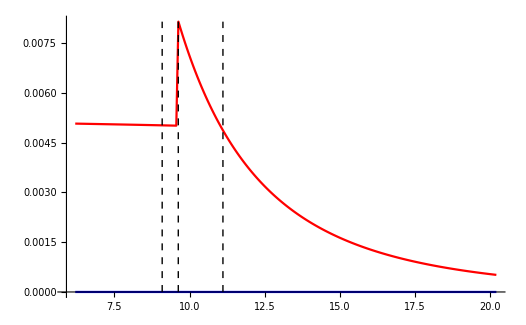

```mathematica
Module[{rmax, rmin, AllData, lineStyle, line1, line2,line3,orbit,t0,r0,θ0,ϕ0, a=0,prec=32,e=0.1,p=10,τmino=0.5},
{rmax, rmin} = OrbitTP[10,0.1];
AllData = Flatten[{Re[Φ0s],Im[Φ0s]}];
lineStyle={Thick,Black,Dashed};
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
line1=Line[{{rmin,Min[AllData]},{rmin,Max[AllData]}}];line2=Line[{{rmax,Min[AllData]},{rmax,Max[AllData]}}];
line3= Line[{{r0[τmino],Min[AllData]},{r0[τmino],Max[AllData]}}];
ListPlot[{Table[{Rs[[i]],Re[Φ0s[[i]]]}, {i,1, Length[Rs]}] , Table[{Rs[[i]], Im[Φ0s[[i]]]},{i,1,Length[Rs]}]}, Joined->True, PlotStyle->{Blue, Red},
Epilog->{Directive[lineStyle],line1,line2,line3}
]
]
```

### l=2 mode

```mathematica
Module[{rmin, rmax,a=0, p=10,e=0.1, τmino=0.5},
{rmax, rmin} = OrbitTP[p,e];
Rs = Subdivide[KerrGeoSeparatrix[a,e,1],rmin+rmax,200];
Φ0s=  Φ0New[a,p,e,τmino,  Rs,2]
]
```

{-1.0842×10^-19-0.00276702 ⅈ,-1.0842×10^-19-0.00279468 ⅈ,-1.6263×10^-19-0.00282205 ⅈ,3.79471×10^-19-0.00284913 ⅈ,-2.98156×10^-19-0.00287593 ⅈ,5.42101×10^-20-0.00290243 ⅈ,-1.6263×10^-19-0.00292865 ⅈ,-5.42101×10^-20-0.00295459 ⅈ,-2.98156×10^-19-0.00298023 ⅈ,1.6263×10^-19-0.00300559 ⅈ,7.04731×10^-19-0.00303067 ⅈ,-1.0842×10^-19-0.00305546 ⅈ,-3.79471×10^-19-0.00307996 ⅈ,-1.0842×10^-19-0.00310418 ⅈ,5.42101×10^-19-0.00312811 ⅈ,2.1684×10^-19-0.00315177 ⅈ,8.67362×10^-19-0.00317513 ⅈ,-1.0842×10^-19-0.00319822 ⅈ,5.42101×10^-20-0.00322102 ⅈ,2.43945×10^-19-0.00324354 ⅈ,4.33681×10^-19-0.00326577 ⅈ,1.35525×10^-19-0.00328772 ⅈ,5.14996×10^-19-0.00330939 ⅈ,1.35525×10^-19-0.00333078 ⅈ,-5.42101×10^-20-0.00335189 ⅈ,-4.33681×10^-19-0.00337272 ⅈ,-5.42101×10^-20-0.00339326 ⅈ,2.71051×10^-20-0.00341353 ⅈ,-5.42101×10^-20-0.00343352 ⅈ,1.6263×10^-19-0.00345322 ⅈ,8.13152×10^-20-0.00347265 ⅈ,2.71051×10^-19-0.00349179 ⅈ,-3.52366×10^-19-0.00351066 ⅈ,0.-0.00352925 ⅈ,6.50521×10^-19-0.00354756 ⅈ,-1.89735×10^-19-0.00356559 ⅈ,-1.6263×10^-19-0.00358335 ⅈ,-1.89735×10^-19-0.00360083 ⅈ,5.69206×10^-19-0.00361803 ⅈ,-1.35525×10^-18-0.00363495 ⅈ,2.43945×10^-19-0.0036516 ⅈ,2.98156×10^-19-0.00366797 ⅈ,-2.43945×10^-19-0.00368407 ⅈ,2.71051×10^-20-0.00369989 ⅈ,-2.71051×10^-20-0.00371543 ⅈ,-1.35525×10^-19-0.0037307 ⅈ,2.71051×10^-19-0.0037457 ⅈ,-6.23416×10^-19-0.00376042 ⅈ,0.-0.00377486 ⅈ,3.61039×10^-17-0.0121828 ⅈ,3.10624×10^-17-0.0118225 ⅈ,3.95734×10^-17-0.0114759 ⅈ,5.53214×10^-17-0.0111424 ⅈ,4.14436×10^-17-0.0108212 ⅈ,4.11726×10^-17-0.010512 ⅈ,4.37747×10^-17-0.0102141 ⅈ,3.75134×10^-17-0.00992707 ⅈ,3.67545×10^-17-0.00965039 ⅈ,2.30664×10^-17-0.00938362 ⅈ,1.08827×10^-17-0.00912633 ⅈ,1.35932×10^-17-0.0088781 ⅈ,2.88262×10^-17-0.00863856 ⅈ,2.71051×10^-17-0.00840733 ⅈ,7.75205×10^-18-0.00818406 ⅈ,1.22379×10^-17-0.00796841 ⅈ,2.75387×10^-17-0.00776008 ⅈ,1.18178×10^-17-0.00755876 ⅈ,1.49891×10^-17-0.00736417 ⅈ,1.35525×10^-19-0.00717602 ⅈ,2.11962×10^-17-0.00699407 ⅈ,2.53161×10^-17-0.00681805 ⅈ,9.81203×10^-18-0.00664775 ⅈ,3.2499×10^-17-0.00648292 ⅈ,2.84874×10^-17-0.00632336 ⅈ,3.24719×10^-17-0.00616886 ⅈ,3.02763×10^-17-0.00601923 ⅈ,1.94072×10^-17-0.00587428 ⅈ,2.18467×10^-17-0.00573382 ⅈ,7.15573×10^-18-0.0055977 ⅈ,2.49502×10^-17-0.00546575 ⅈ,2.88669×10^-18-0.00533781 ⅈ,5.61075×10^-18-0.00521373 ⅈ,3.48774×10^-17-0.00509338 ⅈ,1.3417×10^-17-0.00497661 ⅈ,1.83976×10^-17-0.00486329 ⅈ,5.92245×10^-18-0.00475331 ⅈ,1.31188×10^-17-0.00464653 ⅈ,4.97378×10^-18-0.00454286 ⅈ,1.40946×10^-17-0.00444217 ⅈ,1.90413×10^-17-0.00434436 ⅈ,6.8237×10^-18-0.00424933 ⅈ,8.49066×10^-18-0.00415699 ⅈ,4.87891×10^-18-0.00406724 ⅈ,1.00628×10^-17-0.00397999 ⅈ,2.19415×10^-17-0.00389517 ⅈ,1.32002×10^-17-0.00381267 ⅈ,1.05168×10^-17-0.00373244 ⅈ,9.03954×10^-18-0.00365438 ⅈ,1.05303×10^-17-0.00357844 ⅈ,1.63037×10^-17-0.00350453 ⅈ,1.52059×10^-17-0.0034326 ⅈ,1.2116×10^-17-0.00336258 ⅈ,1.10453×10^-17-0.0032944 ⅈ,8.87691×10^-18-0.00322801 ⅈ,1.06049×10^-17-0.00316335 ⅈ,6.44423×10^-18-0.00310036 ⅈ,1.14112×10^-17-0.003039 ⅈ,7.77915×10^-18-0.0029792 ⅈ,1.48332×10^-17-0.00292093 ⅈ,1.01576×10^-17-0.00286412 ⅈ,6.09864×10^-18-0.00280875 ⅈ,6.94567×10^-18-0.00275476 ⅈ,9.70361×10^-18-0.00270211 ⅈ,6.95922×10^-18-0.00265076 ⅈ,6.3663×10^-18-0.00260068 ⅈ,5.52943×10^-18-0.00255182 ⅈ,9.2767×10^-18-0.00250414 ⅈ,7.71478×10^-18-0.00245761 ⅈ,7.33869×10^-18-0.00241221 ⅈ,5.35325×10^-18-0.00236788 ⅈ,6.44423×10^-18-0.00232461 ⅈ,8.04681×10^-18-0.00228236 ⅈ,6.72883×10^-18-0.0022411 ⅈ,3.47622×10^-18-0.00220081 ⅈ,6.07153×10^-18-0.00216145 ⅈ,6.84403×10^-18-0.002123 ⅈ,7.97566×10^-18-0.00208544 ⅈ,2.41913×10^-18-0.00204873 ⅈ,5.04493×10^-18-0.00201286 ⅈ,5.67851×10^-18-0.0019778 ⅈ,6.38663×10^-18-0.00194353 ⅈ,5.90213×10^-18-0.00191002 ⅈ,6.44761×10^-18-0.00187726 ⅈ,7.45389×10^-18-0.00184523 ⅈ,6.66446×10^-18-0.0018139 ⅈ,3.55076×10^-18-0.00178325 ⅈ,7.73849×10^-18-0.00175328 ⅈ,1.07404×10^-18-0.00172395 ⅈ,4.75694×10^-18-0.00169526 ⅈ,4.92973×10^-18-0.00166718 ⅈ,7.96211×10^-19-0.0016397 ⅈ,3.97428×10^-18-0.00161281 ⅈ,4.49266×10^-18-0.00158648 ⅈ,1.81604×10^-18-0.00156071 ⅈ,4.17757×10^-18-0.00153548 ⅈ,2.80537×10^-18-0.00151077 ⅈ,2.67662×10^-18-0.00148657 ⅈ,7.52165×10^-19-0.00146288 ⅈ,3.08998×10^-18-0.00143967 ⅈ,4.55704×10^-18-0.00141693 ⅈ,3.3678×10^-18-0.00139465 ⅈ,3.5101×10^-18-0.00137283 ⅈ,4.94667×10^-18-0.00135144 ⅈ,3.93193×10^-18-0.00133049 ⅈ,3.52705×10^-18-0.00130995 ⅈ,3.71339×10^-18-0.00128981 ⅈ,4.03865×10^-18-0.00127008 ⅈ,2.67662×10^-18-0.00125073 ⅈ,4.15385×10^-18-0.00123176 ⅈ,2.98494×10^-18-0.00121316 ⅈ,2.79351×10^-18-0.00119492 ⅈ,4.01324×10^-18-0.00117703 ⅈ,3.52874×10^-18-0.00115949 ⅈ,2.49028×10^-18-0.00114228 ⅈ,2.98156×10^-18-0.00112539 ⅈ,2.75794×10^-18-0.00110883 ⅈ,3.41354×10^-18-0.00109258 ⅈ,3.45759×10^-18-0.00107663 ⅈ,2.76133×10^-18-0.00106098 ⅈ,1.17399×10^-18-0.00104562 ⅈ,1.05371×10^-18-0.00103055 ⅈ,4.31987×10^-18-0.00101575 ⅈ,6.06476×10^-19-0.00100123 ⅈ,-4.57398×10^-20-0.000986965 ⅈ,3.01374×10^-18-0.000972963 ⅈ,5.3668×10^-18-0.000959215 ⅈ,1.47723×10^-18-0.000945715 ⅈ,2.41574×10^-18-0.000932456 ⅈ,1.28071×10^-18-0.000919434 ⅈ,2.63597×10^-18-0.000906644 ⅈ,2.78335×10^-18-0.00089408 ⅈ,1.37219×10^-18-0.000881737 ⅈ,2.10064×10^-18-0.000869611 ⅈ,3.63547×10^-18-0.000857696 ⅈ,6.20198×10^-18-0.000845989 ⅈ,3.21873×10^-18-0.000834485 ⅈ,2.83078×10^-18-0.000823179 ⅈ,3.94379×10^-18-0.000812067 ⅈ,4.17587×10^-18-0.000801145 ⅈ,1.70423×10^-18-0.000790409 ⅈ,4.00308×10^-18-0.000779855 ⅈ,1.38744×10^-18-0.000769479 ⅈ,1.27224×10^-18-0.000759278 ⅈ,1.43487×10^-18-0.000749248 ⅈ,5.20078×10^-19-0.000739385 ⅈ,-2.01594×10^-19-0.000729685 ⅈ,1.18585×10^-18-0.000720147 ⅈ,2.05998×10^-18-0.000710765 ⅈ,9.36818×10^-19-0.000701537 ⅈ,3.97258×10^-19-0.00069246 ⅈ,2.64698×10^-18-0.00068353 ⅈ}

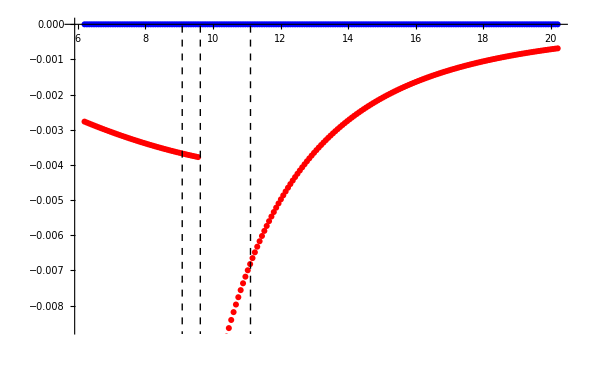

```mathematica
Module[{rmax, rmin, AllData, lineStyle, line1, line2,line3,orbit,t0,r0,θ0,ϕ0, a=0,prec=32,e=0.1,p=10,τmino=0.5},
{rmax, rmin} = OrbitTP[10,0.1];
AllData = Flatten[{Re[Φ0s],Im[Φ0s]}];
lineStyle={Thick,Black,Dashed};
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
line1=Line[{{rmin,Min[AllData]},{rmin,Max[AllData]}}];line2=Line[{{rmax,Min[AllData]},{rmax,Max[AllData]}}];
line3= Line[{{r0[τmino],Min[AllData]},{r0[τmino],Max[AllData]}}];
ListPlot[{Table[{Rs[[i]],Re[Φ0s[[i]]]}, {i,1, Length[Rs]}] , Table[{Rs[[i]], Im[Φ0s[[i]]]},{i,1,Length[Rs]}]}, Joined->False, PlotStyle->{Blue, Red},
Epilog->{Directive[lineStyle],line1,line2,line3}
]
]
```

```mathematica
Module[{rmin, rmax,a=0, p=10,e=0.1, τmino=0.5},
{rmax, rmin} = OrbitTP[p,e];
Rs = Subdivide[KerrGeoSeparatrix[a,e,1],rmin+rmax,200];
Φ0s=  Φ0New[a,p,e,τmino,  Rs,3]
]
```

{-1.6263×10^-19-0.00284572 ⅈ,-1.0842×10^-19-0.00292492 ⅈ,4.87891×10^-19-0.00300524 ⅈ,2.1684×10^-19-0.00308667 ⅈ,-1.0842×10^-19-0.00316922 ⅈ,1.6263×10^-19-0.00325289 ⅈ,-2.1684×10^-19-0.00333768 ⅈ,0.-0.00342358 ⅈ,-1.0842×10^-19-0.00351059 ⅈ,2.1684×10^-19-0.00359872 ⅈ,3.25261×10^-19-0.00368797 ⅈ,-3.25261×10^-19-0.00377832 ⅈ,2.1684×10^-19-0.00386979 ⅈ,-2.1684×10^-19-0.00396237 ⅈ,-5.42101×10^-19-0.00405605 ⅈ,-5.42101×10^-20-0.00415085 ⅈ,5.42101×10^-20-0.00424675 ⅈ,0.-0.00434375 ⅈ,-1.0842×10^-19-0.00444186 ⅈ,0.-0.00454106 ⅈ,4.33681×10^-19-0.00464137 ⅈ,-2.1684×10^-19-0.00474277 ⅈ,1.0842×10^-19-0.00484527 ⅈ,-1.0842×10^-19-0.00494886 ⅈ,2.1684×10^-19-0.00505354 ⅈ,-2.1684×10^-19-0.00515931 ⅈ,-1.0842×10^-18-0.00526617 ⅈ,-9.75782×10^-19-0.00537411 ⅈ,-1.19262×10^-18-0.00548313 ⅈ,5.42101×10^-19-0.00559324 ⅈ,2.1684×10^-19-0.00570441 ⅈ,3.25261×10^-19-0.00581667 ⅈ,5.42101×10^-19-0.00592999 ⅈ,-4.33681×10^-19-0.00604438 ⅈ,4.33681×10^-19-0.00615984 ⅈ,-2.1684×10^-19-0.00627635 ⅈ,-1.0842×10^-19-0.00639393 ⅈ,1.0842×10^-19-0.00651256 ⅈ,4.33681×10^-19-0.00663224 ⅈ,-2.1684×10^-19-0.00675298 ⅈ,0.-0.00687476 ⅈ,8.67362×10^-19-0.00699758 ⅈ,-4.33681×10^-19-0.00712143 ⅈ,3.25261×10^-19-0.00724633 ⅈ,-2.05998×10^-18-0.00737225 ⅈ,8.67362×10^-19-0.0074992 ⅈ,-2.1684×10^-19-0.00762717 ⅈ,1.0842×10^-18-0.00775617 ⅈ,2.1684×10^-19-0.00788617 ⅈ,3.35832×10^-17-0.00105823 ⅈ,-3.89229×10^-17-0.000978858 ⅈ,2.10471×10^-17-0.000904233 ⅈ,3.38×10^-17-0.000834056 ⅈ,-1.62088×10^-17-0.000768048 ⅈ,3.75812×10^-17-0.000705953 ⅈ,1.49078×10^-18-0.00064753 ⅈ,3.24176×10^-17-0.000592554 ⅈ,1.07472×10^-17-0.000540815 ⅈ,3.41795×10^-17-0.000492118 ⅈ,6.47133×10^-17-0.00044628 ⅈ,3.52637×10^-17-0.000403128 ⅈ,-1.1601×10^-17-0.000362504 ⅈ,-6.27482×10^-18-0.000324256 ⅈ,2.16705×10^-17-0.000288246 ⅈ,1.52601×10^-17-0.00025434 ⅈ,9.6765×10^-18-0.000222416 ⅈ,4.5401×10^-17-0.000192359 ⅈ,-9.92045×10^-18-0.000164059 ⅈ,1.6114×10^-17-0.000137417 ⅈ,-1.49688×10^-17-0.000112335 ⅈ,2.28563×10^-17-0.0000887251 ⅈ,-1.75573×10^-17-0.0000665029 ⅈ,-6.21383×10^-18-0.0000455894 ⅈ,3.58464×10^-18-0.0000259105 ⅈ,1.77945×10^-17-7.39646×10^-6 ⅈ,9.02598×10^-18+0.0000100183 ⅈ,6.41712×10^-18+0.0000263954 ⅈ,-3.37458×10^-18+0.0000417929 ⅈ,1.27394×10^-17+0.0000562654 ⅈ,1.9685×10^-17+0.0000698643 ⅈ,1.97325×10^-17+0.0000826381 ⅈ,1.5355×10^-17+0.0000946323 ⅈ,1.41217×10^-17+0.00010589 ⅈ,7.78593×10^-18+0.000116451 ⅈ,4.62277×10^-17+0.000126355 ⅈ,1.54634×10^-17+0.000135637 ⅈ,3.13131×10^-17+0.000144331 ⅈ,2.1081×10^-17+0.000152469 ⅈ,-4.91957×10^-18+0.000160081 ⅈ,-2.28699×10^-17+0.000167196 ⅈ,-1.278×10^-17+0.000173841 ⅈ,-4.64852×10^-18+0.000180042 ⅈ,2.22261×10^-18+0.000185822 ⅈ,1.43623×10^-17+0.000191204 ⅈ,-1.73811×10^-18+0.000196209 ⅈ,1.23091×10^-17+0.000200859 ⅈ,7.72494×10^-19+0.000205171 ⅈ,2.22058×10^-17+0.000209165 ⅈ,1.12147×10^-17+0.000212857 ⅈ,-4.86875×10^-18+0.000216264 ⅈ,6.31209×10^-18+0.0002194 ⅈ,-1.31188×10^-17+0.000222282 ⅈ,1.21058×10^-17+0.000224921 ⅈ,7.84353×10^-18+0.000227332 ⅈ,-4.5096×10^-18+0.000229527 ⅈ,-1.08759×10^-18+0.000231517 ⅈ,1.34712×10^-17+0.000233313 ⅈ,9.92045×10^-18+0.000234926 ⅈ,-1.05371×10^-18+0.000236366 ⅈ,6.87791×10^-18+0.000237642 ⅈ,1.85602×10^-17+0.000238763 ⅈ,1.40336×10^-17+0.000239738 ⅈ,7.21672×10^-18+0.000240574 ⅈ,5.69206×10^-19+0.00024128 ⅈ,2.33103×10^-18+0.000241862 ⅈ,1.1828×10^-17+0.000242327 ⅈ,5.63446×10^-18+0.000242682 ⅈ,-8.49066×10^-18+0.000242933 ⅈ,8.0502×10^-18+0.000243085 ⅈ,5.67173×10^-18+0.000243145 ⅈ,5.09914×10^-18+0.000243117 ⅈ,2.63597×10^-18+0.000243006 ⅈ,4.59092×10^-18+0.000242818 ⅈ,7.84691×10^-18+0.000242556 ⅈ,2.4259×10^-18+0.000242225 ⅈ,5.43456×10^-18+0.000241829 ⅈ,-7.31836×10^-19+0.000241372 ⅈ,-1.51788×10^-18+0.000240857 ⅈ,3.72694×10^-18+0.000240288 ⅈ,7.7927×10^-19+0.000239668 ⅈ,-9.2496×10^-19+0.000239 ⅈ,2.57498×10^-18+0.000238287 ⅈ,4.25549×10^-18+0.000237533 ⅈ,2.71051×10^-18+0.000236739 ⅈ,4.53332×10^-18+0.000235908 ⅈ,-8.13152×10^-19+0.000235042 ⅈ,-1.86347×10^-18+0.000234145 ⅈ,8.53809×10^-19+0.000233217 ⅈ,4.44184×10^-18+0.000232261 ⅈ,7.42001×10^-18+0.00023128 ⅈ,7.46744×10^-18+0.000230274 ⅈ,2.73761×10^-18+0.000229246 ⅈ,7.55553×10^-19+0.000228197 ⅈ,2.76472×10^-18+0.000227129 ⅈ,2.83248×10^-18+0.000226043 ⅈ,2.95106×10^-18+0.00022494 ⅈ,1.06049×10^-18+0.000223823 ⅈ,-1.72795×10^-18+0.000222693 ⅈ,-1.94818×10^-19+0.000221549 ⅈ,-1.33323×10^-18+0.000220395 ⅈ,-6.23416×10^-19+0.00021923 ⅈ,-1.80249×10^-18+0.000218056 ⅈ,1.29427×10^-18+0.000216874 ⅈ,-2.72067×10^-18+0.000215685 ⅈ,3.11708×10^-18+0.00021449 ⅈ,5.88857×10^-18+0.000213288 ⅈ,-1.66018×10^-19+0.000212083 ⅈ,-6.67462×10^-19+0.000210873 ⅈ,-2.05321×10^-18+0.000209659 ⅈ,1.28749×10^-18+0.000208444 ⅈ,2.13113×10^-18+0.000207226 ⅈ,2.79521×10^-18+0.000206007 ⅈ,1.97189×10^-18+0.000204787 ⅈ,-4.87891×10^-19+0.000203566 ⅈ,2.82062×10^-18+0.000202346 ⅈ,1.11639×10^-18+0.000201127 ⅈ,1.12486×10^-18+0.000199909 ⅈ,1.59242×10^-19+0.000198692 ⅈ,-1.72287×10^-18+0.000197477 ⅈ,-1.10792×10^-18+0.000196265 ⅈ,3.18484×10^-19+0.000195055 ⅈ,1.7974×10^-18+0.000193848 ⅈ,2.92396×10^-18+0.000192645 ⅈ,1.21973×10^-19+0.000191445 ⅈ,2.70204×10^-18+0.00019025 ⅈ,1.71778×10^-18+0.000189058 ⅈ,2.60209×10^-18+0.000187871 ⅈ,2.08709×10^-18+0.000186688 ⅈ,2.33781×10^-19+0.000185511 ⅈ,1.10114×10^-18+0.000184338 ⅈ,2.27174×10^-18+0.000183171 ⅈ,2.28699×10^-19+0.000182009 ⅈ,-7.89435×10^-19+0.000180852 ⅈ,-2.77827×10^-19+0.000179702 ⅈ,1.24344×10^-18+0.000178557 ⅈ,1.62461×10^-18+0.000177418 ⅈ,1.55346×10^-18+0.000176285 ⅈ,1.0842×10^-19+0.000175159 ⅈ,2.89008×10^-18+0.000174039 ⅈ,3.01544×10^-19+0.000172925 ⅈ,-1.01305×10^-18+0.000171818 ⅈ,3.22889×10^-18+0.000170717 ⅈ,1.53482×10^-18+0.000169623 ⅈ,1.62292×10^-18+0.000168536 ⅈ,1.90074×10^-18+0.000167455 ⅈ,7.21672×10^-19+0.000166381 ⅈ,2.03288×10^-19+0.000165314 ⅈ,7.2506×10^-19+0.000164254 ⅈ,9.04631×10^-19+0.000163201 ⅈ,4.82809×10^-19+0.000162154 ⅈ,3.15096×10^-19+0.000161115 ⅈ}

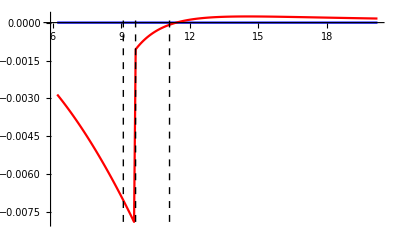

```mathematica
Module[{rmax, rmin, AllData, lineStyle, line1, line2,line3,orbit,t0,r0,θ0,ϕ0, a=0,prec=32,e=0.1,p=10,τmino=0.5},
{rmax, rmin} = OrbitTP[10,0.1];
AllData = Flatten[{Re[Φ0s],Im[Φ0s]}];
lineStyle={Thick,Black,Dashed};
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
line1=Line[{{rmin,Min[AllData]},{rmin,Max[AllData]}}];line2=Line[{{rmax,Min[AllData]},{rmax,Max[AllData]}}];
line3= Line[{{r0[τmino],Min[AllData]},{r0[τmino],Max[AllData]}}];
ListPlot[{Table[{Rs[[i]],Re[Φ0s[[i]]]}, {i,1, Length[Rs]}] , Table[{Rs[[i]], Im[Φ0s[[i]]]},{i,1,Length[Rs]}]}, Joined->True, PlotStyle->{Blue, Red},PlotRange->All,
Epilog->{Directive[lineStyle],line1,line2,line3}
]
]
```

```mathematica
Module[{rmin, rmax,a=0, p=10,e=0.1, τmino=0.5},
{rmax, rmin} = OrbitTP[p,e];
Rs = Subdivide[KerrGeoSeparatrix[a,e,1],rmin+rmax,200];
Φ0s=  Φ0New[a,p,e,τmino,  Rs,4]
]
```

{1.0842×10^-19+0.00315937 ⅈ,0.+0.00328196 ⅈ,-1.0842×10^-19+0.00340741 ⅈ,-1.0842×10^-19+0.00353574 ⅈ,1.0842×10^-19+0.00366696 ⅈ,2.1684×10^-19+0.0038011 ⅈ,1.0842×10^-19+0.00393817 ⅈ,1.0842×10^-19+0.00407819 ⅈ,0.+0.00422118 ⅈ,0.+0.00436714 ⅈ,2.1684×10^-19+0.00451609 ⅈ,-1.0842×10^-19+0.00466806 ⅈ,-4.33681×10^-19+0.00482304 ⅈ,-5.42101×10^-19+0.00498105 ⅈ,3.25261×10^-19+0.00514212 ⅈ,2.1684×10^-19+0.00530623 ⅈ,2.1684×10^-19+0.00547342 ⅈ,-2.1684×10^-19+0.00564369 ⅈ,0.+0.00581704 ⅈ,0.+0.0059935 ⅈ,-2.1684×10^-19+0.00617306 ⅈ,4.33681×10^-19+0.00635573 ⅈ,2.1684×10^-19+0.00654153 ⅈ,2.1684×10^-19+0.00673046 ⅈ,0.+0.00692252 ⅈ,4.33681×10^-19+0.00711773 ⅈ,0.+0.00731608 ⅈ,0.+0.00751759 ⅈ,2.1684×10^-19+0.00772225 ⅈ,-1.0842×10^-18+0.00793007 ⅈ,6.50521×10^-19+0.00814106 ⅈ,-4.33681×10^-19+0.00835521 ⅈ,-2.1684×10^-19+0.00857252 ⅈ,0.+0.00879301 ⅈ,0.+0.00901667 ⅈ,8.67362×10^-19+0.00924349 ⅈ,-4.33681×10^-19+0.00947348 ⅈ,-4.33681×10^-19+0.00970664 ⅈ,2.1684×10^-19+0.00994297 ⅈ,-8.67362×10^-19+0.0101825 ⅈ,-6.50521×10^-19+0.0104251 ⅈ,0.+0.0106709 ⅈ,4.33681×10^-19+0.0109199 ⅈ,0.+0.011172 ⅈ,-1.30104×10^-18+0.0114273 ⅈ,0.+0.0116857 ⅈ,8.67362×10^-19+0.0119472 ⅈ,-8.67362×10^-19+0.0122118 ⅈ,8.67362×10^-19+0.0124796 ⅈ,-9.74274×10^-13+0.0151311 ⅈ,-8.98292×10^-13+0.014441 ⅈ,-8.3086×10^-13+0.013788 ⅈ,-7.71127×10^-13+0.0131697 ⅈ,-7.17817×10^-13+0.0125841 ⅈ,4.02549×10^-13+0.0120291 ⅈ,2.61558×10^-13+0.011503 ⅈ,1.4814×10^-13+0.0110039 ⅈ,5.69788×10^-14+0.0105304 ⅈ,-1.88403×10^-14+0.0100809 ⅈ,-7.64144×10^-14+0.00965396 ⅈ,-1.21676×10^-13+0.00924836 ⅈ,-1.56839×10^-13+0.00886285 ⅈ,-1.83648×10^-13+0.00849629 ⅈ,-2.03556×10^-13+0.00814761 ⅈ,1.77425×10^-12+0.00781581 ⅈ,1.48612×10^-12+0.00749996 ⅈ,1.24113×10^-12+0.00719917 ⅈ,1.03248×10^-12+0.00691262 ⅈ,8.54929×10^-13+0.00663953 ⅈ,7.03919×10^-13+0.00637919 ⅈ,5.75444×10^-13+0.0061309 ⅈ,4.66387×10^-13+0.00589403 ⅈ,3.73796×10^-13+0.00566797 ⅈ,9.42659×10^-14+0.00545216 ⅈ,6.75232×10^-14+0.00524606 ⅈ,4.42167×10^-14+0.00504917 ⅈ,2.39419×10^-14+0.00486101 ⅈ,6.36213×10^-15+0.00468115 ⅈ,-8.88016×10^-15+0.00450916 ⅈ,-2.21529×10^-14+0.00434465 ⅈ,-3.34464×10^-14+0.00418723 ⅈ,-4.31137×10^-14+0.00403657 ⅈ,2.8805×10^-14+0.00389232 ⅈ,1.37386×10^-14+0.00375417 ⅈ,-2.69304×10^-13+0.00362182 ⅈ,-2.50709×10^-13+0.00349501 ⅈ,-2.33939×10^-13+0.00337344 ⅈ,-2.18919×10^-13+0.00325689 ⅈ,-2.05225×10^-13+0.00314511 ⅈ,-1.92812×10^-13+0.00303787 ⅈ,-1.81563×10^-13+0.00293496 ⅈ,-1.71238×10^-13+0.00283618 ⅈ,-1.61847×10^-13+0.00274135 ⅈ,-1.53249×10^-13+0.00265027 ⅈ,-1.91883×10^-13+0.00256278 ⅈ,-1.80245×10^-13+0.00247871 ⅈ,-1.69524×10^-13+0.00239791 ⅈ,-1.59705×10^-13+0.00232023 ⅈ,-1.50682×10^-13+0.00224554 ⅈ,-1.42442×10^-13+0.00217369 ⅈ,-1.34792×10^-13+0.00210458 ⅈ,-1.27746×10^-13+0.00203807 ⅈ,-1.20719×10^-13+0.00197405 ⅈ,-1.12698×10^-13+0.00191242 ⅈ,-1.05215×10^-13+0.00185306 ⅈ,-9.83366×10^-14+0.0017959 ⅈ,-9.19511×10^-14+0.00174082 ⅈ,1.32958×10^-14+0.00168775 ⅈ,6.93977×10^-15+0.0016366 ⅈ,1.63889×10^-15+0.00158729 ⅈ,-2.80499×10^-15+0.00153973 ⅈ,-6.4415×10^-15+0.00149387 ⅈ,-9.44088×10^-15+0.00144963 ⅈ,-1.18463×10^-14+0.00140694 ⅈ,-1.37596×10^-14+0.00136574 ⅈ,-1.52824×10^-14+0.00132598 ⅈ,-1.64152×10^-14+0.00128758 ⅈ,-1.72437×10^-14+0.00125051 ⅈ,-1.78223×10^-14+0.0012147 ⅈ,-1.81899×10^-14+0.0011801 ⅈ,-8.10172×10^-14+0.00114668 ⅈ,-7.35681×10^-14+0.00111437 ⅈ,-6.68877×10^-14+0.00108314 ⅈ,-6.08732×10^-14+0.00105295 ⅈ,-5.54696×10^-14+0.00102376 ⅈ,-5.05855×10^-14+0.000995526 ⅈ,-4.61795×10^-14+0.000968213 ⅈ,-4.22087×10^-14+0.000941788 ⅈ,-3.86147×10^-14+0.000916216 ⅈ,-3.53557×10^-14+0.000891466 ⅈ,-3.23989×10^-14+0.000867507 ⅈ,-2.97118×10^-14+0.00084431 ⅈ,-2.72761×10^-14+0.000821845 ⅈ,-2.50547×10^-14+0.000800088 ⅈ,1.06689×10^-13+0.000779011 ⅈ,9.53124×10^-14+0.00075859 ⅈ,8.51338×10^-14+0.000738802 ⅈ,7.60302×10^-14+0.000719623 ⅈ,6.78889×10^-14+0.000701031 ⅈ,6.0611×10^-14+0.000683006 ⅈ,5.40989×10^-14+0.000665527 ⅈ,4.82814×10^-14+0.000648576 ⅈ,4.30857×10^-14+0.000632134 ⅈ,3.84449×10^-14+0.000616182 ⅈ,3.42995×10^-14+0.000600704 ⅈ,3.0598×10^-14+0.000585684 ⅈ,-6.29783×10^-14+0.000571105 ⅈ,-5.65735×10^-14+0.000556953 ⅈ,-5.08119×10^-14+0.000543213 ⅈ,-4.56357×10^-14+0.000529871 ⅈ,-4.09897×10^-14+0.000516913 ⅈ,-3.68105×10^-14+0.000504327 ⅈ,-3.30458×10^-14+0.0004921 ⅈ,-2.96734×10^-14+0.00048022 ⅈ,-2.66283×10^-14+0.000468676 ⅈ,-2.38901×10^-14+0.000457457 ⅈ,-2.14257×10^-14+0.000446551 ⅈ,-1.92078×10^-14+0.000435949 ⅈ,-1.72148×10^-14+0.000425641 ⅈ,-1.54152×10^-14+0.000415617 ⅈ,-1.37899×10^-14+0.000405867 ⅈ,-1.23302×10^-14+0.000396385 ⅈ,-1.10127×10^-14+0.000387159 ⅈ,-9.82527×10^-15+0.000378184 ⅈ,-8.75246×10^-15+0.000369449 ⅈ,-4.69776×10^-15+0.000360949 ⅈ,-4.05854×10^-15+0.000352676 ⅈ,-3.48322×10^-15+0.000344622 ⅈ,-2.97447×10^-15+0.00033678 ⅈ,-2.51484×10^-15+0.000329145 ⅈ,-2.10421×10^-15+0.00032171 ⅈ,-1.73201×10^-15+0.000314468 ⅈ,-1.39893×10^-15+0.000307413 ⅈ,-1.10414×10^-15+0.000300541 ⅈ,-8.35517×10^-16+0.000293845 ⅈ,-5.94393×10^-16+0.000287321 ⅈ,-2.39628×10^-15+0.000280962 ⅈ,-2.04505×10^-15+0.000274764 ⅈ,-1.79954×10^-14+0.000268723 ⅈ,-1.70815×10^-14+0.000262833 ⅈ,-1.62152×10^-14+0.00025709 ⅈ,-1.53985×10^-14+0.00025149 ⅈ,-1.46462×10^-14+0.000246029 ⅈ,-1.3988×10^-14+0.000240702 ⅈ,-1.33654×10^-14+0.000235506 ⅈ,-1.27749×10^-14+0.000230436 ⅈ,-1.22132×10^-14+0.00022549 ⅈ,-1.16797×10^-14+0.000220664 ⅈ,-1.11754×10^-14+0.000215953 ⅈ,2.32482×10^-15+0.000211356 ⅈ,2.29238×10^-15+0.000206868 ⅈ,2.25547×10^-15+0.000202488 ⅈ,2.19892×10^-15+0.00019821 ⅈ,2.13707×10^-15+0.000194034 ⅈ,2.07558×10^-15+0.000189956 ⅈ,2.01695×10^-15+0.000185972 ⅈ,1.95803×10^-15+0.000182082 ⅈ,1.90219×10^-15+0.000178281 ⅈ,1.8449×10^-15+0.000174568 ⅈ,1.79138×10^-15+0.00017094 ⅈ,1.73913×10^-15+0.000167395 ⅈ}

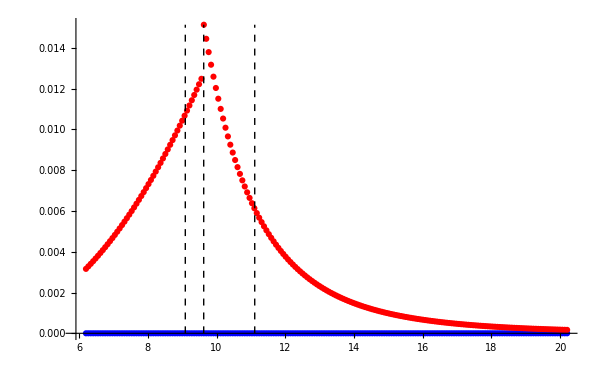

```mathematica
Module[{rmax, rmin, AllData, lineStyle, line1, line2,line3,orbit,t0,r0,θ0,ϕ0, a=0,prec=32,e=0.1,p=10,τmino=0.5},
{rmax, rmin} = OrbitTP[10,0.1];
AllData = Flatten[{Re[Φ0s],Im[Φ0s]}];
lineStyle={Thick,Black,Dashed};
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
line1=Line[{{rmin,Min[AllData]},{rmin,Max[AllData]}}];line2=Line[{{rmax,Min[AllData]},{rmax,Max[AllData]}}];
line3= Line[{{r0[τmino],Min[AllData]},{r0[τmino],Max[AllData]}}];
ListPlot[{Table[{Rs[[i]],Re[Φ0s[[i]]]}, {i,1, Length[Rs]}] , Table[{Rs[[i]], Im[Φ0s[[i]]]},{i,1,Length[Rs]}]}, Joined->False, PlotStyle->{Blue, Red},PlotRange->All,
Epilog->{Directive[lineStyle],line1,line2,line3}
]
]
```

## Plotting Φ_2

#### Sum over l

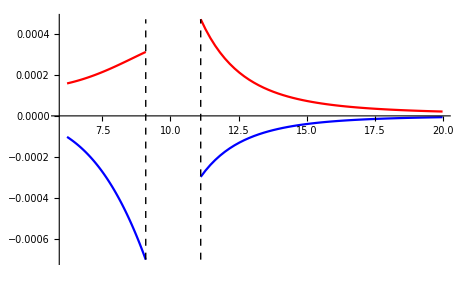

```mathematica
Module[{rmin, rmax,a=0, p=10,e=0.1, τmino=0.5},
{rmax, rmin} = OrbitTP[p,e];
lowerRs =Subdivide[KerrGeoSeparatrix[a,e,1], rmin, 50];
upperRs = Subdivide[rmax, 20,50];
lowerΦ2 = Monitor[Table[Φ2 [a , lowerRs[[i]] ,τmino, p,e],{i,1 ,Length[lowerRs]}],i];
upperΦ2 =Monitor[Table[Φ2 [a , upperRs[[i]] ,τmino, p,e],{i,1 ,Length[lowerRs]}],50+i];
]
Module[{rmax, rmin, AllData, lineStyle, line1, line2},
{rmax, rmin} = OrbitTP[10,0.1];
AllData = Flatten[{Re[lowerΦ2],Im[lowerΦ2], Re[upperΦ2],Im[upperΦ2]}];
lineStyle={Thick,Black,Dashed};
line1=Line[{{rmin,Min[AllData]},{rmin,Max[AllData]}}];line2=Line[{{rmax,Min[AllData]},{rmax,Max[AllData]}}];
ListPlot[{Table[{lowerRs[[i]], Re[lowerΦ2[[i]]]},{i, 1 Length[lowerRs]}],Table[{lowerRs[[i]], Im[lowerΦ2[[i]]]},{i, 1 Length[lowerRs]}],Table[{upperRs[[i]], Re[upperΦ2[[i]]]},{i, 1 Length[upperRs]}],Table[{upperRs[[i]], Im[upperΦ2[[i]]]},{i, 1 Length[upperRs]}] }, Joined->True, PlotStyle->{Blue, Red,Blue,Red},
Epilog->{Directive[lineStyle],line1,line2}
]
]
```

Haas(2012) and  Thesis by Patrick Nolan (UCD)

### l = 1 mode

```mathematica
Module[{rmin, rmax,a=0, p=10,e=0.1, τmino=0.5},
{rmax, rmin} = OrbitTP[p,e];
Rs = Subdivide[KerrGeoSeparatrix[a,e,1],rmin+rmax,200];
Φ2s=  Φ2[a,p,e,τmino,  Rs,1]
]
```

{-1.01644×10^-20+0.00178792 ⅈ,0.+0.0017967 ⅈ,0.+0.00180525 ⅈ,-3.38813×10^-21+0.00181359 ⅈ,1.01644×10^-20+0.00182173 ⅈ,-6.43745×10^-20+0.00182966 ⅈ,-3.04932×10^-20+0.0018374 ⅈ,3.38813×10^-21+0.00184495 ⅈ,-3.04932×10^-20+0.00185231 ⅈ,-2.37169×10^-20+0.0018595 ⅈ,-3.04932×10^-20+0.00186651 ⅈ,-2.71051×10^-20+0.00187336 ⅈ,2.03288×10^-20+0.00188004 ⅈ,3.04932×10^-20+0.00188657 ⅈ,2.71051×10^-20+0.00189294 ⅈ,1.35525×10^-20+0.00189917 ⅈ,-1.35525×10^-20+0.00190525 ⅈ,0.+0.00191118 ⅈ,-2.03288×10^-20+0.00191699 ⅈ,0.+0.00192265 ⅈ,3.38813×10^-20+0.00192819 ⅈ,-6.77626×10^-21+0.0019336 ⅈ,3.38813×10^-21+0.00193889 ⅈ,-2.71051×10^-20+0.00194406 ⅈ,0.+0.00194911 ⅈ,6.77626×10^-21+0.00195404 ⅈ,3.04932×10^-20+0.00195887 ⅈ,1.35525×10^-20+0.00196359 ⅈ,2.71051×10^-20+0.0019682 ⅈ,-6.77626×10^-21+0.0019727 ⅈ,1.35525×10^-20+0.00197711 ⅈ,-3.38813×10^-21+0.00198142 ⅈ,-1.69407×10^-20+0.00198564 ⅈ,1.69407×10^-20+0.00198976 ⅈ,-2.37169×10^-20+0.00199378 ⅈ,-3.04932×10^-20+0.00199772 ⅈ,0.+0.00200158 ⅈ,-1.69407×10^-20+0.00200534 ⅈ,2.03288×10^-20+0.00200902 ⅈ,1.69407×10^-20+0.00201263 ⅈ,1.01644×10^-20+0.00201615 ⅈ,-3.38813×10^-21+0.00201959 ⅈ,1.01644×10^-20+0.00202296 ⅈ,6.77626×10^-21+0.00202625 ⅈ,6.77626×10^-21+0.00202947 ⅈ,-3.04932×10^-20+0.00203262 ⅈ,-1.69407×10^-20+0.0020357 ⅈ,3.38813×10^-21+0.0020387 ⅈ,1.35525×10^-20+0.00204165 ⅈ,-7.74779×10^-16+0.0013846 ⅈ,4.4609×10^-15+0.00135486 ⅈ,4.3596×10^-15+0.00132598 ⅈ,4.27016×10^-15+0.00129795 ⅈ,4.18182×10^-15+0.00127072 ⅈ,4.09043×10^-15+0.00124426 ⅈ,4.00027×10^-15+0.00121856 ⅈ,3.91642×10^-15+0.00119358 ⅈ,3.83425×10^-15+0.00116931 ⅈ,3.74473×10^-15+0.0011457 ⅈ,3.67317×10^-15+0.00112275 ⅈ,3.59007×10^-15+0.00110042 ⅈ,3.50859×10^-15+0.00107871 ⅈ,3.43844×10^-15+0.00105758 ⅈ,3.37174×10^-15+0.00103701 ⅈ,3.29318×10^-15+0.001017 ⅈ,3.23389×10^-15+0.000997516 ⅈ,3.16179×10^-15+0.000978544 ⅈ,3.09141×10^-15+0.000960068 ⅈ,3.0342×10^-15+0.000942072 ⅈ,2.96698×10^-15+0.000924541 ⅈ,2.90307×10^-15+0.000907459 ⅈ,2.85187×10^-15+0.000890812 ⅈ,2.4377×10^-15+0.000874586 ⅈ,2.30533×10^-15+0.000858769 ⅈ,4.26525×10^-15+0.000843347 ⅈ,2.43887×10^-15+0.000828308 ⅈ,2.41618×10^-15+0.000813641 ⅈ,2.37122×10^-15+0.000799333 ⅈ,2.3363×10^-15+0.000785375 ⅈ,2.30939×10^-15+0.000771755 ⅈ,2.26883×10^-15+0.000758464 ⅈ,2.2336×10^-15+0.00074549 ⅈ,2.23621×10^-15+0.000732827 ⅈ,2.19537×10^-15+0.000720462 ⅈ,2.14964×10^-15+0.00070839 ⅈ,2.11356×10^-15+0.000696599 ⅈ,2.07821×10^-15+0.000685083 ⅈ,2.05016×10^-15+0.000673834 ⅈ,2.00568×10^-15+0.000662844 ⅈ,1.97002×10^-15+0.000652105 ⅈ,1.93447×10^-15+0.00064161 ⅈ,1.89704×10^-15+0.000631353 ⅈ,2.18414×10^-15+0.000621327 ⅈ,1.77044×10^-15+0.000611526 ⅈ,1.74902×10^-15+0.000601943 ⅈ,1.7301×10^-15+0.000592571 ⅈ,1.70638×10^-15+0.000583407 ⅈ,1.48233×10^-15+0.000574443 ⅈ,1.48285×10^-15+0.000565674 ⅈ,1.47863×10^-15+0.000557096 ⅈ,1.476×10^-15+0.000548703 ⅈ,1.46993×10^-15+0.00054049 ⅈ,1.45444×10^-15+0.000532452 ⅈ,1.44608×10^-15+0.000524585 ⅈ,1.43403×10^-15+0.000516884 ⅈ,1.41365×10^-15+0.000509345 ⅈ,1.39765×10^-15+0.000501964 ⅈ,1.38266×10^-15+0.000494736 ⅈ,1.36546×10^-15+0.000487658 ⅈ,1.34986×10^-15+0.000480726 ⅈ,1.332×10^-15+0.000473936 ⅈ,1.30711×10^-15+0.000467285 ⅈ,1.2934×10^-15+0.000460769 ⅈ,1.2745×10^-15+0.000454385 ⅈ,1.25558×10^-15+0.000448129 ⅈ,1.23874×10^-15+0.000441999 ⅈ,2.69206×10^-15+0.00043599 ⅈ,1.20784×10^-15+0.000430101 ⅈ,1.18748×10^-15+0.000424328 ⅈ,1.16864×10^-15+0.000418669 ⅈ,1.15261×10^-15+0.000413121 ⅈ,1.13573×10^-15+0.00040768 ⅈ,1.11514×10^-15+0.000402345 ⅈ,1.1018×10^-15+0.000397113 ⅈ,1.08628×10^-15+0.000391982 ⅈ,1.07113×10^-15+0.000386949 ⅈ,1.05164×10^-15+0.000382011 ⅈ,1.03613×10^-15+0.000377168 ⅈ,1.01931×10^-15+0.000372416 ⅈ,1.25939×10^-15+0.000367753 ⅈ,9.56219×10^-16+0.000363177 ⅈ,9.49525×10^-16+0.000358687 ⅈ,9.3589×10^-16+0.00035428 ⅈ,9.2643×10^-16+0.000349955 ⅈ,9.13173×10^-16+0.000345709 ⅈ,9.02513×10^-16+0.000341541 ⅈ,8.94084×10^-16+0.00033745 ⅈ,8.79127×10^-16+0.000333432 ⅈ,8.71082×10^-16+0.000329488 ⅈ,8.55472×10^-16+0.000325614 ⅈ,8.45836×10^-16+0.00032181 ⅈ,8.31811×10^-16+0.000318074 ⅈ,8.22234×10^-16+0.000314405 ⅈ,8.09325×10^-16+0.000310801 ⅈ,7.97275×10^-16+0.000307261 ⅈ,7.85691×10^-16+0.000303783 ⅈ,7.74417×10^-16+0.000300366 ⅈ,7.64826×10^-16+0.000297008 ⅈ,7.56044×10^-16+0.000293709 ⅈ,7.42025×10^-16+0.000290468 ⅈ,7.32647×10^-16+0.000287282 ⅈ,7.22565×10^-16+0.000284151 ⅈ,7.10927×10^-16+0.000281074 ⅈ,7.02344×10^-16+0.00027805 ⅈ,6.92518×10^-16+0.000275077 ⅈ,6.8014×10^-16+0.000272154 ⅈ,6.7309×10^-16+0.000269281 ⅈ,6.64256×10^-16+0.000266456 ⅈ,6.54303×10^-16+0.000263678 ⅈ,6.44039×10^-16+0.000260947 ⅈ,6.3847×10^-16+0.000258262 ⅈ,6.2713×10^-16+0.000255621 ⅈ,6.18906×10^-16+0.000253023 ⅈ,6.10347×10^-16+0.000250469 ⅈ,6.0114×10^-16+0.000247956 ⅈ,2.29899×10^-16+0.000245485 ⅈ,6.1558×10^-16+0.000243054 ⅈ,6.0787×10^-16+0.000240662 ⅈ,6.01913×10^-16+0.000238309 ⅈ,5.9373×10^-16+0.000235994 ⅈ,5.86195×10^-16+0.000233717 ⅈ,5.80154×10^-16+0.000231476 ⅈ,1.1405×10^-15+0.000229271 ⅈ,1.04036×10^-15+0.0002271 ⅈ,1.01643×10^-15+0.000224965 ⅈ,4.96275×10^-16+0.000222863 ⅈ,4.88165×10^-16+0.000220794 ⅈ,4.83879×10^-16+0.000218758 ⅈ,4.7618×10^-16+0.000216754 ⅈ,2.25486×10^-16+0.000214781 ⅈ,4.74435×10^-16+0.000212839 ⅈ,4.69014×10^-16+0.000210927 ⅈ,4.62991×10^-16+0.000209045 ⅈ,4.57909×10^-16+0.000207192 ⅈ,4.50552×10^-16+0.000205367 ⅈ,4.46221×10^-16+0.00020357 ⅈ,4.40802×10^-16+0.000201801 ⅈ,4.34469×10^-16+0.000200059 ⅈ,4.28746×10^-16+0.000198343 ⅈ,4.23383×10^-16+0.000196653 ⅈ,4.18672×10^-16+0.000194989 ⅈ,4.1265×10^-16+0.00019335 ⅈ,4.0902×10^-16+0.000191735 ⅈ,4.03278×10^-16+0.000190145 ⅈ,3.97957×10^-16+0.000188578 ⅈ,3.92279×10^-16+0.000187035 ⅈ,3.87776×10^-16+0.000185515 ⅈ,3.83322×10^-16+0.000184017 ⅈ,3.77332×10^-16+0.000182542 ⅈ,3.72815×10^-16+0.000181088 ⅈ,3.70469×10^-16+0.000179655 ⅈ}

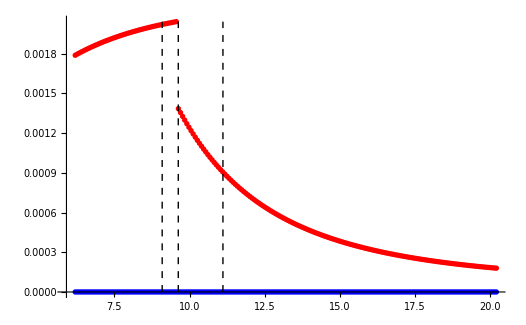

```mathematica
Module[{rmax, rmin, AllData, lineStyle, line1, line2,line3,orbit,t0,r0,θ0,ϕ0, a=0,prec=32,e=0.1,p=10,τmino=0.5},
{rmax, rmin} = OrbitTP[10,0.1];
AllData = Flatten[{Re[Φ2s],Im[Φ2s]}];
lineStyle={Thick,Black,Dashed};
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
line1=Line[{{rmin,Min[AllData]},{rmin,Max[AllData]}}];line2=Line[{{rmax,Min[AllData]},{rmax,Max[AllData]}}];
line3= Line[{{r0[τmino],Min[AllData]},{r0[τmino],Max[AllData]}}];
ListPlot[{Table[{Rs[[i]],Re[Φ2s[[i]]]}, {i,1, Length[Rs]}] , Table[{Rs[[i]], Im[Φ2s[[i]]]},{i,1,Length[Rs]}]}, Joined->False, PlotStyle->{Blue, Red},
Epilog->{Directive[lineStyle],line1,line2,line3}
]
]
```

### l=2 mode

```mathematica
Module[{rmin, rmax,a=0, p=10,e=0.1, τmino=0.5},
{rmax, rmin} = OrbitTP[p,e];
Rs = Subdivide[KerrGeoSeparatrix[a,e,1],rmin+rmax,200];
Φ2s=  Φ2[a,p,e,τmino,  Rs,2]
]
```

{5.42101×10^-20-0.00119708 ⅈ,7.45389×10^-20-0.00122094 ⅈ,-6.77626×10^-20-0.00124488 ⅈ,-1.28749×10^-19-0.00126889 ⅈ,1.89735×10^-19-0.00129298 ⅈ,0.-0.00131715 ⅈ,1.0842×10^-19-0.00134139 ⅈ,7.45389×10^-20-0.0013657 ⅈ,-4.06576×10^-20-0.00139009 ⅈ,-2.71051×10^-20-0.00141455 ⅈ,2.71051×10^-20-0.00143909 ⅈ,-1.49078×10^-19-0.00146369 ⅈ,0.-0.00148836 ⅈ,-1.35525×10^-20-0.0015131 ⅈ,-2.71051×10^-20-0.00153791 ⅈ,6.77626×10^-20-0.00156279 ⅈ,5.42101×10^-20-0.00158773 ⅈ,-5.42101×10^-20-0.00161274 ⅈ,6.77626×10^-20-0.00163781 ⅈ,6.77626×10^-20-0.00166295 ⅈ,0.-0.00168815 ⅈ,0.-0.00171341 ⅈ,-1.35525×10^-20-0.00173874 ⅈ,-5.42101×10^-20-0.00176412 ⅈ,-8.13152×10^-20-0.00178957 ⅈ,1.35525×10^-20-0.00181507 ⅈ,-1.0842×10^-19-0.00184063 ⅈ,4.06576×10^-20-0.00186626 ⅈ,5.42101×10^-20-0.00189193 ⅈ,9.48677×10^-20-0.00191767 ⅈ,1.21973×10^-19-0.00194346 ⅈ,5.42101×10^-20-0.00196931 ⅈ,-5.42101×10^-20-0.00199521 ⅈ,-1.21973×10^-19-0.00202117 ⅈ,2.43945×10^-19-0.00204718 ⅈ,1.35525×10^-20-0.00207324 ⅈ,6.77626×10^-20-0.00209936 ⅈ,1.35525×10^-20-0.00212552 ⅈ,1.89735×10^-19-0.00215174 ⅈ,5.42101×10^-20-0.00217801 ⅈ,-8.13152×10^-20-0.00220433 ⅈ,-1.35525×10^-19-0.00223069 ⅈ,8.13152×10^-20-0.00225711 ⅈ,0.-0.00228357 ⅈ,-1.0842×10^-19-0.00231009 ⅈ,-1.6263×10^-19-0.00233664 ⅈ,8.13152×10^-20-0.00236325 ⅈ,-2.71051×10^-20-0.0023899 ⅈ,0.-0.00241659 ⅈ,-4.09716×10^-15-0.000598728 ⅈ,-3.95266×10^-15-0.000575667 ⅈ,-3.85686×10^-15-0.00055355 ⅈ,-3.762×10^-15-0.000532332 ⅈ,-3.63247×10^-15-0.000511972 ⅈ,-3.51598×10^-15-0.00049243 ⅈ,-3.44908×10^-15-0.000473668 ⅈ,-3.3278×10^-15-0.00045565 ⅈ,-3.25783×10^-15-0.000438342 ⅈ,-3.16461×10^-15-0.000421713 ⅈ,-3.09341×10^-15-0.000405731 ⅈ,-2.99993×10^-15-0.000390369 ⅈ,-2.91613×10^-15-0.000375598 ⅈ,-2.83318×10^-15-0.000361392 ⅈ,-2.78721×10^-15-0.000347727 ⅈ,-2.70969×10^-15-0.000334579 ⅈ,-2.61591×10^-15-0.000321926 ⅈ,-2.54757×10^-15-0.000309747 ⅈ,-2.50619×10^-15-0.000298021 ⅈ,-2.42714×10^-15-0.000286729 ⅈ,-2.3693×10^-15-0.000275854 ⅈ,-2.31449×10^-15-0.000265376 ⅈ,-2.26332×10^-15-0.000255281 ⅈ,-2.2158×10^-15-0.000245551 ⅈ,-2.16012×10^-15-0.000236172 ⅈ,-2.08822×10^-15-0.00022713 ⅈ,-2.05554×10^-15-0.000218411 ⅈ,-1.9986×10^-15-0.000210002 ⅈ,-1.95626×10^-15-0.00020189 ⅈ,-1.89677×10^-15-0.000194064 ⅈ,-1.86205×10^-15-0.000186511 ⅈ,-1.81702×10^-15-0.000179222 ⅈ,-1.77636×10^-15-0.000172186 ⅈ,-1.73158×10^-15-0.000165393 ⅈ,-1.68685×10^-15-0.000158834 ⅈ,-1.64168×10^-15-0.000152499 ⅈ,-1.61462×10^-15-0.00014638 ⅈ,-1.57999×10^-15-0.000140469 ⅈ,-1.55218×10^-15-0.000134758 ⅈ,-1.51829×10^-15-0.000129238 ⅈ,-1.48327×10^-15-0.000123904 ⅈ,-1.46258×10^-15-0.000118748 ⅈ,-1.4218×10^-15-0.000113763 ⅈ,-1.3782×10^-15-0.000108943 ⅈ,-1.35563×10^-15-0.000104282 ⅈ,-1.32462×10^-15-0.0000997739 ⅈ,-1.29856×10^-15-0.0000954136 ⅈ,-1.2746×10^-15-0.0000911955 ⅈ,-1.24597×10^-15-0.0000871143 ⅈ,-1.21947×10^-15-0.0000831653 ⅈ,-1.1933×10^-15-0.0000793436 ⅈ,-1.16618×10^-15-0.0000756447 ⅈ,-1.14534×10^-15-0.0000720644 ⅈ,-1.10989×10^-15-0.0000685983 ⅈ,-1.09774×10^-15-0.0000652425 ⅈ,-1.07533×10^-15-0.0000619931 ⅈ,-1.05299×10^-15-0.0000588465 ⅈ,-1.02896×10^-15-0.000055799 ⅈ,-1.01155×10^-15-0.0000528473 ⅈ,-9.96912×10^-16-0.0000499881 ⅈ,-9.75634×10^-16-0.0000472181 ⅈ,-9.5722×10^-16-0.0000445345 ⅈ,-9.34029×10^-16-0.0000419343 ⅈ,-9.24044×10^-16-0.0000394146 ⅈ,-9.01044×10^-16-0.0000369727 ⅈ,-8.81853×10^-16-0.0000346062 ⅈ,-8.67451×10^-16-0.0000323124 ⅈ,-8.53181×10^-16-0.0000300889 ⅈ,-8.35215×10^-16-0.0000279336 ⅈ,-8.19684×10^-16-0.000025844 ⅈ,-8.06239×10^-16-0.0000238181 ⅈ,-7.92211×10^-16-0.0000218538 ⅈ,-7.75944×10^-16-0.0000199491 ⅈ,-7.61056×10^-16-0.0000181022 ⅈ,-7.45549×10^-16-0.000016311 ⅈ,-7.32069×10^-16-0.000014574 ⅈ,-7.24526×10^-16-0.0000128892 ⅈ,-7.06289×10^-16-0.0000112552 ⅈ,-7.02297×10^-16-9.67027×10^-6 ⅈ,-6.82956×10^-16-8.13288×10^-6 ⅈ,-6.70829×10^-16-6.64156×10^-6 ⅈ,-6.58881×10^-16-5.19487×10^-6 ⅈ,-6.4598×10^-16-3.79143×10^-6 ⅈ,-6.38025×10^-16-2.42991×10^-6 ⅈ,-6.24245×10^-16-1.10902×10^-6 ⅈ,-6.14395×10^-16+1.72479×10^-7 ⅈ,-6.02532×10^-16+1.4158×10^-6 ⅈ,-5.96851×10^-16+2.62208×10^-6 ⅈ,-5.83345×10^-16+3.79246×10^-6 ⅈ,-5.73195×10^-16+4.92801×10^-6 ⅈ,-5.62969×10^-16+6.02978×10^-6 ⅈ,-5.55291×10^-16+7.09877×10^-6 ⅈ,-5.43548×10^-16+8.13596×10^-6 ⅈ,-5.36164×10^-16+9.14229×10^-6 ⅈ,-5.28959×10^-16+0.0000101187 ⅈ,-5.18914×10^-16+0.000011066 ⅈ,-5.12347×10^-16+0.0000119851 ⅈ,-5.01972×10^-16+0.0000128767 ⅈ,-4.9182×10^-16+0.0000137418 ⅈ,-4.83692×10^-16+0.0000145811 ⅈ,-4.7951×10^-16+0.0000153953 ⅈ,-4.74023×10^-16+0.000016185 ⅈ,-4.58397×10^-16+0.0000169512 ⅈ,-4.53266×10^-16+0.0000176943 ⅈ,-4.47596×10^-16+0.0000184151 ⅈ,-4.41165×10^-16+0.0000191141 ⅈ,-4.36061×10^-16+0.0000197921 ⅈ,-4.29054×10^-16+0.0000204495 ⅈ,-4.22841×10^-16+0.000021087 ⅈ,-4.14493×10^-16+0.0000217051 ⅈ,-4.06288×10^-16+0.0000223044 ⅈ,-4.03421×10^-16+0.0000228853 ⅈ,-3.95934×10^-16+0.0000234484 ⅈ,-3.89758×10^-16+0.0000239941 ⅈ,-3.83268×10^-16+0.000024523 ⅈ,-3.75213×10^-16+0.0000250355 ⅈ,-3.72034×10^-16+0.000025532 ⅈ,-3.67475×10^-16+0.000026013 ⅈ,-3.60474×10^-16+0.0000264788 ⅈ,-3.57522×10^-16+0.00002693 ⅈ,-3.5334×10^-16+0.0000273668 ⅈ,-3.4297×10^-16+0.0000277896 ⅈ,-3.43579×10^-16+0.000028199 ⅈ,-3.35067×10^-16+0.000028595 ⅈ,-3.29717×10^-16+0.0000289783 ⅈ,-3.25651×10^-16+0.0000293489 ⅈ,-3.19598×10^-16+0.0000297074 ⅈ,-3.15452×10^-16+0.000030054 ⅈ,-3.12214×10^-16+0.000030389 ⅈ,-3.07789×10^-16+0.0000307127 ⅈ,-3.02808×10^-16+0.0000310254 ⅈ,-2.9826×10^-16+0.0000313274 ⅈ,-2.94404×10^-16+0.000031619 ⅈ,-2.90044×10^-16+0.0000319003 ⅈ,-2.8722×10^-16+0.0000321718 ⅈ,-2.817×10^-16+0.0000324336 ⅈ,-2.79643×10^-16+0.0000326859 ⅈ,-2.73522×10^-16+0.0000329291 ⅈ,-2.69446×10^-16+0.0000331632 ⅈ,-2.67535×10^-16+0.0000333887 ⅈ,-2.61514×10^-16+0.0000336056 ⅈ,-2.60063×10^-16+0.0000338142 ⅈ,-2.56814×10^-16+0.0000340146 ⅈ,-2.52417×10^-16+0.0000342072 ⅈ,-2.50035×10^-16+0.000034392 ⅈ,-2.46399×10^-16+0.0000345692 ⅈ,-2.42708×10^-16+0.0000347392 ⅈ,-2.39833×10^-16+0.0000349019 ⅈ,-2.35062×10^-16+0.0000350576 ⅈ,-2.32608×10^-16+0.0000352065 ⅈ,-2.30232×10^-16+0.0000353487 ⅈ,-2.2624×10^-16+0.0000354843 ⅈ}

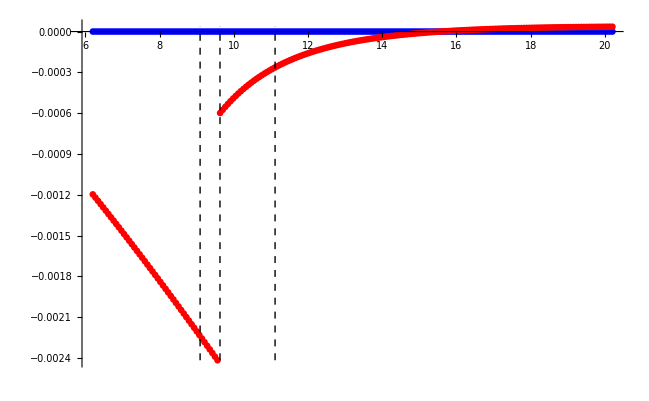

```mathematica
Module[{rmax, rmin, AllData, lineStyle, line1, line2,line3,orbit,t0,r0,θ0,ϕ0, a=0,prec=32,e=0.1,p=10,τmino=0.5},
{rmax, rmin} = OrbitTP[10,0.1];
AllData = Flatten[{Re[Φ2s],Im[Φ2s]}];
lineStyle={Thick,Black,Dashed};
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
line1=Line[{{rmin,Min[AllData]},{rmin,Max[AllData]}}];line2=Line[{{rmax,Min[AllData]},{rmax,Max[AllData]}}];
line3= Line[{{r0[τmino],Min[AllData]},{r0[τmino],Max[AllData]}}];
ListPlot[{Table[{Rs[[i]],Re[Φ2s[[i]]]}, {i,1, Length[Rs]}] , Table[{Rs[[i]], Im[Φ2s[[i]]]},{i,1,Length[Rs]}]}, Joined->False, PlotStyle->{Blue, Red},
Epilog->{Directive[lineStyle],line1,line2,line3}, PlotRange->All
]
]
```

```mathematica
Module[{rmin, rmax,a=0, p=10,e=0.1, τmino=0.5},
{rmax, rmin} = OrbitTP[p,e];
Rs = Subdivide[KerrGeoSeparatrix[a,e,1],rmin+rmax,200];
Φ2s=  Φ2[a,p,e,τmino,  Rs,3]
]
```

{4.74338×10^-20-0.000250877 ⅈ,-1.35525×10^-20-0.000256587 ⅈ,-6.77626×10^-21-0.000262263 ⅈ,-6.09864×10^-20-0.000267901 ⅈ,-1.35525×10^-20-0.000273497 ⅈ,6.09864×10^-20-0.000279047 ⅈ,-6.77626×10^-21-0.000284546 ⅈ,1.15196×10^-19-0.00028999 ⅈ,-6.77626×10^-20-0.000295375 ⅈ,-1.35525×10^-20-0.000300697 ⅈ,5.42101×10^-20-0.000305952 ⅈ,-1.28749×10^-19-0.000311135 ⅈ,-6.09864×10^-20-0.000316241 ⅈ,-1.35525×10^-20-0.000321268 ⅈ,-5.42101×10^-20-0.000326211 ⅈ,1.35525×10^-20-0.000331065 ⅈ,6.77626×10^-21-0.000335826 ⅈ,1.21973×10^-19-0.00034049 ⅈ,2.71051×10^-20-0.000345053 ⅈ,1.21973×10^-19-0.00034951 ⅈ,-2.43945×10^-19-0.000353858 ⅈ,-1.76183×10^-19-0.000358092 ⅈ,6.77626×10^-20-0.000362207 ⅈ,1.35525×10^-20-0.000366201 ⅈ,-1.35525×10^-19-0.000370068 ⅈ,-1.89735×10^-19-0.000373804 ⅈ,-2.71051×10^-20-0.000377405 ⅈ,3.52366×10^-19-0.000380867 ⅈ,2.71051×10^-20-0.000384186 ⅈ,0.-0.000387357 ⅈ,0.-0.000390377 ⅈ,-1.21973×10^-19-0.000393241 ⅈ,0.-0.000395944 ⅈ,-4.06576×10^-20-0.000398484 ⅈ,0.-0.000400855 ⅈ,-8.13152×10^-20-0.000403053 ⅈ,6.77626×10^-20-0.000405075 ⅈ,-5.42101×10^-20-0.000406916 ⅈ,1.35525×10^-20-0.000408572 ⅈ,1.35525×10^-20-0.000410039 ⅈ,-1.49078×10^-19-0.000411312 ⅈ,1.0842×10^-19-0.000412389 ⅈ,2.30393×10^-19-0.000413263 ⅈ,9.48677×10^-20-0.000413932 ⅈ,-9.48677×10^-20-0.000414392 ⅈ,8.13152×10^-20-0.000414637 ⅈ,1.0842×10^-19-0.000414665 ⅈ,-2.30393×10^-19-0.00041447 ⅈ,-2.71051×10^-20-0.00041405 ⅈ,-1.59055×10^-14-0.00187274 ⅈ,-1.5314×10^-14-0.00180955 ⅈ,-1.47222×10^-14-0.00174902 ⅈ,-1.41496×10^-14-0.00169103 ⅈ,-1.37269×10^-14-0.00163545 ⅈ,-1.31954×10^-14-0.00158215 ⅈ,-1.27012×10^-14-0.00153104 ⅈ,-1.22315×10^-14-0.001482 ⅈ,-1.18126×10^-14-0.00143493 ⅈ,-1.13562×10^-14-0.00138974 ⅈ,-1.09588×10^-14-0.00134634 ⅈ,-1.05782×10^-14-0.00130464 ⅈ,-1.0207×10^-14-0.00126457 ⅈ,-9.8921×10^-15-0.00122606 ⅈ,-9.54624×10^-15-0.00118902 ⅈ,-9.20923×10^-15-0.0011534 ⅈ,-8.87591×10^-15-0.00111912 ⅈ,-8.587×10^-15-0.00108613 ⅈ,-8.30857×10^-15-0.00105438 ⅈ,-8.04555×10^-15-0.0010238 ⅈ,-7.77104×10^-15-0.000994341 ⅈ,-7.49443×10^-15-0.00096596 ⅈ,-7.29106×10^-15-0.000938608 ⅈ,-7.05717×10^-15-0.000912241 ⅈ,-6.81586×10^-15-0.000886815 ⅈ,-6.60149×10^-15-0.000862292 ⅈ,-6.37968×10^-15-0.000838634 ⅈ,-6.20046×10^-15-0.000815803 ⅈ,-6.00351×10^-15-0.000793767 ⅈ,-5.79869×10^-15-0.000772491 ⅈ,-5.6262×10^-15-0.000751945 ⅈ,-5.45875×10^-15-0.000732099 ⅈ,-5.29542×10^-15-0.000712924 ⅈ,-5.13133×10^-15-0.000694395 ⅈ,-4.97791×10^-15-0.000676484 ⅈ,-4.82581×10^-15-0.000659167 ⅈ,-4.69747×10^-15-0.000642421 ⅈ,-4.55574×10^-15-0.000626224 ⅈ,-4.41971×10^-15-0.000610554 ⅈ,-4.29457×10^-15-0.00059539 ⅈ,-4.16574×10^-15-0.000580714 ⅈ,-4.04907×10^-15-0.000566507 ⅈ,-3.92644×10^-15-0.00055275 ⅈ,-3.82035×10^-15-0.000539427 ⅈ,-3.70272×10^-15-0.000526522 ⅈ,-3.59739×10^-15-0.000514019 ⅈ,-3.50006×10^-15-0.000501902 ⅈ,-3.40727×10^-15-0.000490159 ⅈ,-3.31642×10^-15-0.000478775 ⅈ,-3.22568×10^-15-0.000467737 ⅈ,-3.13306×10^-15-0.000457033 ⅈ,-3.04611×10^-15-0.000446651 ⅈ,-2.96662×10^-15-0.000436578 ⅈ,-2.88303×10^-15-0.000426805 ⅈ,-2.80177×10^-15-0.00041732 ⅈ,-2.73112×10^-15-0.000408114 ⅈ,-2.65497×10^-15-0.000399177 ⅈ,-2.58993×10^-15-0.000390499 ⅈ,-2.52117×10^-15-0.000382071 ⅈ,-2.45013×10^-15-0.000373885 ⅈ,-2.3866×10^-15-0.000365933 ⅈ,-2.33527×10^-15-0.000358207 ⅈ,-2.27062×10^-15-0.000350699 ⅈ,-2.21141×10^-15-0.000343401 ⅈ,-2.1667×10^-15-0.000336308 ⅈ,-2.10204×10^-15-0.000329411 ⅈ,-2.04937×10^-15-0.000322705 ⅈ,-1.99624×10^-15-0.000316183 ⅈ,-1.95146×10^-15-0.000309839 ⅈ,-1.89871×10^-15-0.000303668 ⅈ,-1.84983×10^-15-0.000297663 ⅈ,-1.80693×10^-15-0.00029182 ⅈ,-1.76215×10^-15-0.000286134 ⅈ,-1.71721×10^-15-0.000280599 ⅈ,-1.67716×10^-15-0.000275211 ⅈ,-1.64135×10^-15-0.000269964 ⅈ,-1.59148×10^-15-0.000264855 ⅈ,-1.55737×10^-15-0.00025988 ⅈ,-1.5189×10^-15-0.000255034 ⅈ,-1.48309×10^-15-0.000250312 ⅈ,-1.4483×10^-15-0.000245713 ⅈ,-1.41416×10^-15-0.000241231 ⅈ,-1.37808×10^-15-0.000236863 ⅈ,-1.34615×10^-15-0.000232606 ⅈ,-1.31852×10^-15-0.000228456 ⅈ,-1.28636×10^-15-0.00022441 ⅈ,-1.25955×10^-15-0.000220465 ⅈ,-1.22642×10^-15-0.000216619 ⅈ,-1.20333×10^-15-0.000212868 ⅈ,-1.17154×10^-15-0.000209209 ⅈ,-1.14366×10^-15-0.000205639 ⅈ,-1.12036×10^-15-0.000202157 ⅈ,-1.09769×10^-15-0.00019876 ⅈ,-1.07035×10^-15-0.000195444 ⅈ,-1.04841×10^-15-0.000192209 ⅈ,-1.02623×10^-15-0.000189051 ⅈ,-1.00169×10^-15-0.000185968 ⅈ,-9.77676×10^-16-0.000182959 ⅈ,-9.55955×10^-16-0.000180021 ⅈ,-9.35103×10^-16-0.000177152 ⅈ,-9.16613×10^-16-0.000174351 ⅈ,-8.96755×10^-16-0.000171615 ⅈ,-8.77375×10^-16-0.000168942 ⅈ,-8.58905×10^-16-0.000166332 ⅈ,-8.39078×10^-16-0.000163781 ⅈ,-8.21076×10^-16-0.000161289 ⅈ,-8.04969×10^-16-0.000158855 ⅈ,-7.8645×10^-16-0.000156475 ⅈ,-7.70841×10^-16-0.00015415 ⅈ,-7.53517×10^-16-0.000151877 ⅈ,-7.37969×10^-16-0.000149655 ⅈ,-7.22295×10^-16-0.000147484 ⅈ,-7.08075×10^-16-0.00014536 ⅈ,-6.9095×10^-16-0.000143284 ⅈ,-6.77789×10^-16-0.000141254 ⅈ,-6.6274×10^-16-0.000139269 ⅈ,-6.50048×10^-16-0.000137327 ⅈ,-6.36837×10^-16-0.000135428 ⅈ,-6.23742×10^-16-0.00013357 ⅈ,-6.1014×10^-16-0.000131752 ⅈ,-5.97287×10^-16-0.000129974 ⅈ,-5.85715×10^-16-0.000128235 ⅈ,-5.74077×10^-16-0.000126532 ⅈ,-5.62062×10^-16-0.000124867 ⅈ,-5.52049×10^-16-0.000123236 ⅈ,-5.39858×10^-16-0.000121641 ⅈ,-5.29525×10^-16-0.000120079 ⅈ,-5.18446×10^-16-0.00011855 ⅈ,-5.08659×10^-16-0.000117053 ⅈ,-4.98163×10^-16-0.000115588 ⅈ,-4.87809×10^-16-0.000114153 ⅈ,-4.78464×10^-16-0.000112748 ⅈ,-4.68283×10^-16-0.000111372 ⅈ,-4.60262×10^-16-0.000110025 ⅈ,-4.50189×10^-16-0.000108705 ⅈ,-4.41882×10^-16-0.000107412 ⅈ,-4.32647×10^-16-0.000106146 ⅈ,-4.2459×10^-16-0.000104906 ⅈ,-4.15942×10^-16-0.000103691 ⅈ,-4.07807×10^-16-0.0001025 ⅈ,-4.00496×10^-16-0.000101334 ⅈ,-3.92403×10^-16-0.000100191 ⅈ,-3.84715×10^-16-0.0000990707 ⅈ,-3.77712×10^-16-0.0000979729 ⅈ,-3.69607×10^-16-0.0000968971 ⅈ,-3.62959×10^-16-0.0000958425 ⅈ,-3.56498×10^-16-0.0000948089 ⅈ,-3.49475×10^-16-0.0000937956 ⅈ,-3.42944×10^-16-0.0000928023 ⅈ,-3.36484×10^-16-0.0000918284 ⅈ,-3.29752×10^-16-0.0000908735 ⅈ,-3.2296×10^-16-0.0000899373 ⅈ}

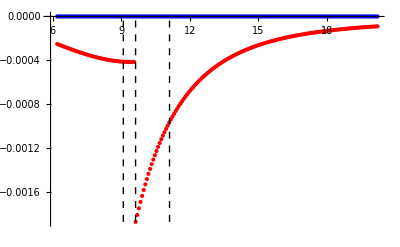

```mathematica
Module[{rmax, rmin, AllData, lineStyle, line1, line2,line3,orbit,t0,r0,θ0,ϕ0, a=0,prec=32,e=0.1,p=10,τmino=0.5},
{rmax, rmin} = OrbitTP[10,0.1];
AllData = Flatten[{Re[Φ2s],Im[Φ2s]}];
lineStyle={Thick,Black,Dashed};
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
line1=Line[{{rmin,Min[AllData]},{rmin,Max[AllData]}}];line2=Line[{{rmax,Min[AllData]},{rmax,Max[AllData]}}];
line3= Line[{{r0[τmino],Min[AllData]},{r0[τmino],Max[AllData]}}];
ListPlot[{Table[{Rs[[i]],Re[Φ2s[[i]]]}, {i,1, Length[Rs]}] , Table[{Rs[[i]], Im[Φ2s[[i]]]},{i,1,Length[Rs]}]}, Joined->False, PlotStyle->{Blue, Red},
Epilog->{Directive[lineStyle],line1,line2,line3}, PlotRange->All
]
]
```